```mathematica
Options[CompareEstimators]={PolarArgs-> None,CEArgs->None,ExpTiltArgs->None,AKArgs->None,HazTwistArgs-> None,SLNArgs->None,Verbosity->1,TestName-> None,TrueVals-> None};

SimulateTruncated[𝒟_,lb_,R_]:=Module[{𝒟PRec,t,U,FTruncInv,x,OutputPrec=6},
𝒟PRec=SetPrecision[𝒟,∞];
U=RandomVariate[UniformDistribution[{0,(1-CDF[𝒟PRec,t])}/.{t-> lb}],R,WorkingPrecision->30];
FTruncInv=Refine[InverseCDF[𝒟PRec,CDF[𝒟PRec,lb]+x],x>0 && x <(1-CDF[𝒟PRec,lb])];
Map[N[FTruncInv /. {x-> #},OutputPrec]&,U]
];

(* The Dirichlet distribution sometimes generates angles which are numerically 0. or 1. (i.e. on the axes). Mathematica then says these points have a PDF of 0. If this happens, evaluate the PDF at a slightly perturbed value. *)
PDFofDirichlet[u_,θ_]:=Boole[Total[θ]==1]*
If[MemberQ[θ,0.]|| MemberQ[θ,1.],
PDF[DirichletDistribution[u],((θ+10^-10)/Total[θ+10^-10])[[;;-2]]],
PDF[DirichletDistribution[u],θ[[;;-2]]]];

(* Preliminaries for the Weibull Sum example. *)
WeibullSumDistribution[d_,β_]:=Module[{SumSF,SummandD,f,λ,λPrime,fSum},
SumSF=((2β π)/(β-1))^((d-1)/2)d^(-1/2)(x/d)^(β(d-1)/2)Exp[-d (x/d)^β] ; 
(* Note: SF only starts "working" (i.e. decreasing) at x >= 2^(-1/β) (1-1/d)^(1/β) d. *)
Return[ProbabilityDistribution[{"SF",SumSF},{x,0.0,∞}]]
];

(* http://mathematica.stackexchange.com/questions/69771/implement-the-bisection-algorithm-elegantly-and-easily *)
biSection[func_,{a_,b_},eps_?Positive]/;(a<b&&func[a]func[b]<0):=Module[{c=a,d=b},With[{test=If[func[a]>0,Greater,Less]},While[d-c>eps,With[{e=(c+d)/2},If[test[func[e],0],c=e,d=e]]];
{c,d}]]



VectorisedNewtonsMethod[fn_,targets_,niter_,min_:None]:=Module[{update,xs,todo,diffs},

xs=ConstantArray[Indeterminate,Length[targets]];

update[x_,t_]=FullSimplify[(fn[x]-t)/D[fn[x],x]];
todo=Range[Length[xs]];

Do[
If[Mod[rep,5]== 0,Print["Starting Newton with ",Length[todo], " components to finish"]];

xs[[todo]]=min+RandomVariate[ExponentialDistribution[1],Length[todo]];

Do[
Quiet[
xs[[todo]]=xs[[todo]] -update[xs[[todo]],targets[[todo]]]
,{General::unfl ,General::ovfl}];
,{i,niter}];

todo=Select[Range[Length[xs]],
xs[[#]]===Indeterminate||xs[[#]]===Underflow[]||xs[[#]]===Overflow[]||Im[xs[[#]]]≠ 0|| xs[[#]]<min& ];

If[Length[todo]== 0, Break[]];

,{rep,50}];

xs];

VectorisedHalleysMethod[fn_,targets_,niter_,min_:None]:=Module[{update,xs,todo,diffs},

xs=ConstantArray[Indeterminate,Length[targets]];

update[x_,t_]=FullSimplify[(fn[x]-t)/fn'[x](1+((fn[x]-t)fn''[x])/(2 fn'[x]^2))];
todo=Range[Length[xs]];

Do[
xs[[todo]]=min+RandomVariate[ExponentialDistribution[1],Length[todo]];

Do[
Quiet[
xs[[todo]]=xs[[todo]] -update[xs[[todo]],targets[[todo]]]
,{General::unfl ,General::ovfl}];
,{i,niter}];

todo=Select[Range[Length[xs]],
xs[[#]]===Indeterminate||xs[[#]]===Underflow[]||xs[[#]]===Overflow[]||Im[xs[[#]]]≠ 0|| xs[[#]]<min& ];

If[Length[todo]== 0, Break[]];

,{rep,50}];

xs];

SimulateTruncatedWeibull[𝒟_,d_,β_,lb_,R_]:=Module[{𝒟PRec,t,U,FTruncInv,x,OutputPrec=6},
𝒟PRec=SetPrecision[𝒟,∞];
U=RandomVariate[UniformDistribution[{1-SurvivalFunction[𝒟PRec,lb],0.999999}],R];

Table[x/.FindRoot[1-((2β π)/(β-1))^((d-1)/2)d^(-1/2)(x/d)^(β(d-1)/2)Exp[-d (x/d)^β]== U[[r]],{x,10}],{r,R}]
];


(* Proposal distribution for the exponentially-tilted Weibull distribution. *)
WeibullTiltedProposals[d_,γs_,Marginals_]:=Module[{β=Marginals[[1]][[1]],AMs,ASDs},
(* Calculate the means & sd's for the asymptotic normal approximation to the tilted distribution. *)
AMs=Table[γ/d,{γ,γs}];
ASDs=Table[1/Sqrt[ β(β-1) E^(-(γ/d)^β)],{γ,γs}];
Table[GammaDistribution[(AMs[[i]]/ASDs[[i]])^2,ASDs[[i]]^2/AMs[[i]]],{i,Length[γs]}]
];


WeibullAngleSetup[𝒟_]:=Module[{d,Marg,β,λDash,ω,ρ,NormDist,XDist,AngleDist,Simulate,PDFEval},
d=Length[RandomVariate[𝒟]];
Marg=MarginalDistribution[𝒟,1];
β=Marg[[1]];

λDash[x_]=β (β-1)x^(β-2);

If[d==2,
λDash[x_]=β (β-1)x^(β-2);
AngleDist=Function[γ,SetPrecision[BetaDistribution[(γ^2 λDash[γ/d])/d^2-1/d,(γ^2 λDash[γ/d])/d^2-1/d],20]];
Simulate[Ss_]:=Table[RandomVariate[AngleDist[s]],{s,Ss}];
PDFEval[Ss_,θs_]:=Table[PDF[AngleDist[Ss[[i]]],θs[[i,1]]],{i,Length[Ss]}];

Return[{Simulate,PDFEval}]
];

ω[x_]=√(2β(β-1)(x/d)^(β-2));

ρ=-1/(d-1);

NormDist=MultinormalDistribution[ConstantArray[0,d-1],(1-ρ)*IdentityMatrix[d-1]+ρ];

XDist=Function[γ,TransformedDistribution[
Table[Subscript[W, i],{i,d-1}]/ω[γ]+γ/d,Table[Subscript[W, i],{i,d-1}]\[Distributed]NormDist]];

AngleDist=Function[γ,TransformedDistribution[Table[Subscript[X, i],{i,d-1}]/γ,Table[Subscript[X, i],{i,d-1}]\[Distributed]XDist[γ]]];

Simulate[Ss_]:=
RandomVariate[NormDist,Length[Ss]]/(Ss*ω[Ss])+1/d;

PDFEval[Ss_,θs_]:=Table[PDF[AngleDist[Ss[[i]]],θs[[i,1;;d-1]]],{i,Length[Ss]}];

{Simulate,PDFEval}
];


SubexpIIDSetup[𝒟_]:=Module[{d,Marg,θDist,Simulate,PDFEval},
d=Length[RandomVariate[𝒟]];
Marg=MarginalDistribution[𝒟,1];

Simulate[Ss_]:=RandomVariate[Marg, {Length[Ss],d-1}] /Ss;

PDFEval[Ss_,θs_]:=Module[{Assum=Table[Subscript[θ, i]>0,{i,d}]~Join~{s>0},
tr=Transpose[θs],ScaledPDFs,Symb, Repl,Valid},
Valid=Map[Boole[#>0]&,tr[[-1]]];

ScaledPDFs=Refine[Table[s PDF[Marg,s Subscript[θ, i]],{i,d}],Assum];
Symb=Mean[Table[Fold[Times,Delete[ScaledPDFs,k]],{k,d}]];

Repl= Table[Subscript[θ, i]-> tr[[i]],{i,d}] ~ Join ~ {s-> Ss};
Valid*Flatten[Re[Symb /. Repl]]
];

{Simulate,PDFEval}
];

SubexpIndSetup[𝒟_]:=Module[{d,Margs,DropWeights,θDist,Simulate,PDFEval},
d=Length[RandomVariate[𝒟]];

Margs=Table[MarginalDistribution[𝒟,i],{i,d}];

(* Calculate weights for which we select a specific component to be the pseudo-maximum. *)
DropWeights[Ss_]:=Module[{Dr},Dr=Transpose@Table[SurvivalFunction[Margs[[i]],Ss],{i,d}];
Dr/(Dr.ConstantArray[1, d])
];

Simulate[Ss_]:= Module[{θs,Dr, DropInds},
θs=Transpose[Map[RandomVariate[#, Length[Ss]] &,Margs]]/Ss;
Dr=DropWeights[Ss];
DropInds=Table[RandomChoice[Dr[[r]]-> Range[d]],{r,Length[Ss]}];

Do[
θs[[r,DropInds[[r]]]]=1-Total[Delete[θs[[r]],DropInds[[r]]]],
{r,Length[Ss]}];

θs
];

PDFEval[Ss_,θs_]:=Module[{Dr,ScaledPDFs,F,θSym=Table[Subscript[θ, i],{i,d}], θSymValid=Table[Subscript[θ, i]>0,{i,d}]~ Join ~ {s>0},
tr=Transpose[θs],Symb, Repl,Valid},

Valid=Map[Boole[#>0]&,Min /@ θs];

ScaledPDFs=Refine[Table[s PDF[Margs[[i]],s Subscript[θ, i]],{i,d}],θSymValid];

Symb=Table[Fold[Times,Delete[ScaledPDFs,k]],{k,d}];
Repl= Table[Subscript[θ, i]-> tr[[i]],{i,d}] ~ Join ~ {s-> Ss};

F=Transpose@Re[Symb /. Repl];
Dr=DropWeights[Ss];

Valid*((Dr*F).ConstantArray[1,d])
];

{Simulate,PDFEval}
];

IndPDF[Margs_,xs_]:=Module[{trXs=Transpose[xs],d=Length[Margs],pdfs},
pdfs=Table[PDF[Margs[[i]],trXs[[i]]],{i,d}];
Flatten@Product[pdfs[[i]],{i,d}]
];

CopPDF[Copula_,Margs_,xs_]:=Module[{trXs=Transpose[xs],d=Length[Margs],us, cdfs,joint},
us=Table[CDF[Margs[[i]],trXs[[i]]],{i,d}];
joint=GetJointPDF[Copula,Margs];
joint/.Join[Table[Subscript[u, i]-> us[[i]],{i,d}],Table[Subscript[x, i]-> trXs[[i]],{i,d}]]
];

IsIndCopula[Copula_]:=(Copula=== "Product");

GetCopulaInfo[Copula_]:=Module[{ϕ,ψ,CopulaName,θ},
If[Copula=!="Product",
{CopulaName,θ}=Copula;
Switch[CopulaName,
"Clayton",
ϕ[u_]=(1+u/θ)^-θ;
ψ[u_]=θ (u^(-1/θ)-1);
,
"Frank",
ϕ[u_]=1/Log[θ] Log[1+Exp[-u] (Exp[Log[θ]]-1)];
ψ[u_]=-Log[ (Exp[Log[θ] u] - 1)/(Exp[Log[θ]]-1)],
"GumbelHougaard",
ϕ[u_]=Exp[-u^(1/θ)];
ψ[u_]=(-Log[u])^θ;
,
_,
ϕ=None;ψ=None
]];
{ϕ,ψ}
];

GetPDFsCDFs[Margs_]:=Module[{n=Length[Margs],LBs,UBs,PDFs,CDFs},
(* Extract the simple form for the pdfs/cdfs assuming the input is inside the relevant support. *)
LBs=Table[Quantile[Margs[[i]],0],{i,n}];UBs=Table[Quantile[Margs[[i]],1],{i,n}];
PDFs=Table[Refine[PDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];
CDFs=Table[Refine[CDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];
{PDFs,CDFs}
];

GetJointPDF[Copula_,Margs_]:=Module[{n=Length[Margs]},
(* Calculate the pdf of X using properties of Archimedean copulas *)
Block[{ϕ,ψ,ZDist,CPDF,IndPDF},
{ϕ,ψ}=GetCopulaInfo[Copula];
CPDF=If[IsIndCopula[Copula],1,
(D[ϕ[t],{t,n}]/.{t-> Sum[ψ[Subscript[u, i]],{i,n}]})*Product[ψ'[Subscript[u, i]],{i,n}]
];

IndPDF=Product[pdf,{pdf,First@GetPDFsCDFs[Margs]}];
IndPDF*CPDF
]
];

AKEstimator[d_,γs_,Args_,Verbosity_:1]:=Module[{𝒟=Args["𝒟"],R=Lookup[Args,"R",10^4],Ests,CCDFs,RVs,RV,γ,Tails,Indices,startTime,Copula,Margs,t,CondTails,ϕ,ψ,PDFs,CDFs,Others,ϕDeriv,CondCDF,Est,XMinusi,i},

Copula=𝒟[[1]];
Margs=Table[MarginalDistribution[𝒟,i],{i,d}];
CCDFs=Table[SurvivalFunction[MarginalDistribution[𝒟,i]],{i,d}];

t=First@AbsoluteTiming[
CondTails=If[IsIndCopula[Copula],
Table[1-Subscript[u, i],{i,d}],
{ϕ,ψ}=GetCopulaInfo[Copula];
{PDFs,CDFs}=GetPDFsCDFs[Margs];
Table[
Others=DeleteCases[Range[d],i];

(* Find the conditional cdf of Subscript[X, i] | Subscript[X, Others] *)
ϕDeriv=D[ϕ[t],{t,d-1}];
CondCDF=(ϕDeriv/.{t->Sum[ψ[Subscript[u, i]],{i,d}]})/(ϕDeriv/.{t-> Sum[ψ[Subscript[u, i]],{i,Others}]});
1-CondCDF
,{i,d}]
];
];

If[t>1,Print["(AK) Calculating derivatives took: ",  t]];

Transpose[Table[
γ=γs[[g]];
If[Verbosity ≥ 2,Print["[AKEstimator] Estimating P(S > ",γ,")…"]];

startTime=AbsoluteTime[];

Tails=Table[CCDFs[[i]][γ],{i,d}] // #/Total[#] &//N;

t=First@AbsoluteTiming[RVs=RandomVariate[𝒟,R];];
If[t>1,Print["(AK) Simulating took: ",  t]];

Indices=RandomChoice[Tails->Range[d],R];
t=First@AbsoluteTiming[Ests=Table[
i=Indices[[r]];
Others=DeleteCases[Range[d],i];
XMinusi=Delete[RVs[[r]],i];
Est=CondTails[[i]]/Tails[[i]]/.Join[ {Subscript[u, i]->CDF[Margs[[i]], Max[Max[XMinusi],γ-Total[XMinusi]]]},Table[Subscript[u, j]->CDF[Margs[[j]],RVs[[r,j]]],{j,Others}]];
Est
,{r,R}];
];

Ests=DeleteCases[Ests,Indeterminate];

If[t>1,Print["(AK) Main estimation took: ",  t]];

{Mean[Ests],StandardDeviation[Ests]/(Sqrt[Length[Ests]]*Mean[Ests]), AbsoluteTime[]-startTime}
,{g,Length[γs]}]]
];

HazFun[𝒟_,x_]:= −Log[SurvivalFunction[𝒟,x]];
HazardTwistedInvCDF[𝒟_,θ_,y_]:= InverseCDF[𝒟,1 - (1-y)^(-1/(θ-1))];
HazardTwistedLR[𝒟_,θ_,x_]:=Exp[-θ HazFun[𝒟,x]]/(1-θ);

HazTwistEstimator[d_,γs_,Args_,Verbosity_:1]:=Module[{𝒟=Args["𝒟"],R=Lookup[Args,"R",10^4],Twist=Lookup[Args,"Twist","All"],Prec=Lookup[Args,"Prec",20],Marginals,θ,θs,γ,Tails,TwistInds,startTime=AbsoluteTime[],setupTime,Samples,W,Ests,Us},

(* Extract the marginal distributions. *)
Marginals=Table[MarginalDistribution[𝒟,i],{i,d}];

(* The indices which will be Hazard rate twisted. *)
TwistInds=Switch[Twist,"All",
Range[d],
"Heavy",
Tails=Table[SurvivalFunction[Marginals[[i]],Max[10^6,Max[γs]]],{i,d}];
Position[Tails,Max[Tails]],
"First",
{1}
];
If[Verbosity≥ 2, Print["[HazTwist] Components selected: ", TwistInds]];

setupTime=AbsoluteTime[]-startTime;

Transpose[Table[
startTime=AbsoluteTime[];
γ=γs[[g]];

(* Calculated the 'twisted' θ. *)
θ=1-(Length[TwistInds]/HazFun[Marginals[[First[TwistInds]]],γ]);

(* The θ for each component (a '0' means that the component is not twisted). *)
θs=Table[If[MemberQ[TwistInds,i],θ,0],{i,d}];

If[Verbosity≥ 2,Print["[HazTwist] Twist amount: ",θs]];
Us=RandomVariate[UniformDistribution[],{d,R},WorkingPrecision->20];
Samples=N[Transpose[Table[HazardTwistedInvCDF[Marginals[[i]],θs[[i]],Us[[i]]],{i,d}]],10];

If[Verbosity≥ 2,Print["[HazTwist] Some samples: ", Samples[[1;;Min[5,Length[Samples]]]]]];
If[Verbosity≥ 2,Print["[HazTwist] Num infinite: ",Count[Samples,∞,2]]];


W[x_,θs_]:= Product[HazardTwistedLR[Marginals[[i]],θs[[i]],x[[i]]],{i,d}];
Ests=Map[If[Count[#,∞] > 0,Indeterminate, Boole[Total[#] > γ]W[#,θs]]&,Samples];
Ests=DeleteCases[Ests,Indeterminate];
If[Verbosity≥ 2,Print["[HazTwist] P(S > ",γ,") estimate: ", Mean[Ests]]];

{Mean[Ests],StandardDeviation[Ests]/(Sqrt[R]*Mean[Ests]),setupTime+AbsoluteTime[]-startTime},{g,Length[γs]}]]]



ExpTilt[f_,d_,γs_,Args_,Verbosity_:1]:=Module[{startTime,𝒟,R,Marginals,β,λ,DD,DSum,θ,MGF,TiltPDF,DDTiltedProposal,TiltCDF,RQuant,ProposalDist,AsymNormMean,AsymNormSD,Dist,CC,Numers,Denoms,Keep,Xs,Xs2,LRs,Sums2,Ests,TiltProp,Proposals,LHS,t,αs,βs,γ,𝒟New,g,Samples},

𝒟=Args["𝒟"];R=Args["R"];

TiltProp=Lookup[Args,"TiltProp",None];
Marginals=Table[MarginalDistribution[𝒟,i],{i,d}];

LHS=Total[Map[D[Log@MomentGeneratingFunction[#,t],{t}] &,Marginals]];


Switch[Marginals[[1,0]],
(* Exponential tilting for the light-tailed Weibull distribution. *)
 WeibullDistribution,

β=Marginals[[1,1]];
λ[y_]=β y^(β-1);

DD=Marginals[[1]];
DSum=𝒟;

Transpose@Table[
startTime=AbsoluteTime[];

θ=λ[x/d];
If[Verbose,Print["θ = ", θ]];

MGF=
MomentGeneratingFunction[DD,θ];

TiltPDF[y_]=E^(θ y) PDF[DD,y]/MGF;

AsymNormMean=x/d;
AsymNormSD=1/Sqrt[λ'[x/d]];

ProposalDist=GammaDistribution[(AsymNormMean/AsymNormSD)^2,AsymNormSD^2/AsymNormMean];
RQuant=4*x;
CC=Quiet@First@FindMaximum[{TiltPDF[y]/PDF[ProposalDist,y],y>0 && y < RQuant},{y,AsymNormMean},MaxIterations->300];

If[CC < 1, CC=2];

If[Verbosity≥ 3,Print["A-R constant: ", CC]];

Xs=RandomVariate[ProposalDist,Min[Ceiling[R*d*CC],10^7]];
If[Verbosity≥3,Print["Number of summands: ", Length[Xs], " Wanted: ", R*d*CC]];
Numers=Map[TiltPDF[#]&,Xs];
Denoms=Map[CC*PDF[ProposalDist,#]&,Xs];
Keep=Select[Range[Length[Xs]],RandomReal[]<Numers[[#]]/Denoms[[#]]&];
If[Verbosity≥3,Print["Accept: ",N[ Length[Keep]/Length[Xs]]]];
Keep=Take[Keep,Min[R*d,Length[Keep]]];
If[Verbosity≥ 3,Print["Effective R: ", Length[Flatten[Keep]], " wanted: ",  R*d]];

Xs2=ArrayReshape[Xs[[Keep]],{R,d}];
LRs=Re@Map[E^(-θ #) *MGF&,Xs2,{2}];
LRs=Map[Fold[Times,#]&,LRs];
Sums2=Total[Transpose[Xs2]];

Ests=Table[Boole[Sums2[[i]]>x]*LRs[[i]],{i,R}];

{Mean[Ests],StandardDeviation[Ests]/(Sqrt[R]*Mean[Ests]),AbsoluteTime[]-startTime}
,{x,γs}],
(* Exponential tilting for Gamma distribution. *)
GammaDistribution,

αs=Map[#[[1]] &, Marginals];
βs=Map[#[[2]] &, Marginals];

Transpose[Table[
startTime=AbsoluteTime[];
γ=γs[[ind]];
(*θ=Max[Min[ Flatten[{t}/.NSolve[LHS== γ ,{t}]]],0];*)

θ=Max[Min[ Flatten[{t}/.FindRoot[LHS== γ ,{t,1}]]],0];

If[Verbosity≥ 1,
Print["[ExpTilt] θ = ", θ]];

Proposals=Table[GammaDistribution[αs[[i]],(βs[[i]]^-1-θ)^-1],{i,d}];

𝒟New=CopulaDistribution["Product",Proposals];

g[x_]:=PDF[𝒟New,x];

Samples=RandomVariate[𝒟New,R,WorkingPrecision->30];
Ests=Map[Boole[Total[#]>γ]*f[#]/g[#]&, Samples];
{Mean[Ests],StandardDeviation[Ests]/(Sqrt[R]*Mean[Ests]),setupTime+AbsoluteTime[]-startTime}
,{ind,Length[γs]}]],
_,
Print["Can't (I don't think) handle things that aren't Weibull or Gamma distributions for exponential tilting yet."];
None
]
];

AsymptoticEstimator[γs_,AsymptoticArgs_]:=Module[{G,S},
Subscript[Ḡ, S][γ_]:= SurvivalFunction[AsymptoticArgs["𝒟G_S"],γ];
Transpose[Map[Reverse[AbsoluteTiming[AsymptoticArgs["c_S"]  Subscript[Ḡ, S][#]]]&,γs]]
];

BigTheta[Xs_,g_]:=Module[{Ss,Inds,Big},
If[Length[Xs]== 0,Return[{}]];
Ss=Total[Transpose[Xs]];
Inds=Select[Range[Length[Ss]],Ss[[#]]>g&];
Xs[[Inds,;;-2]] / Ss[[Inds]]
];

BigX[Xs_,g_]:=Module[{Ss,Inds,Big},
If[Length[Xs]== 0,Return[{}]];
Ss=Total[Transpose[Xs]];
Xs[[Select[Range[Length[Ss]],Ss[[#]]>g&]]]
];

AllIndices[d_,n_]:=Flatten[Permutations[PadRight[#,d]]&/@IntegerPartitions[n,d],1];
BernsteinMixture[𝒟_,d_,γ_,n_]:=Module[{vs,ws},
vs= AllIndices[d,n];
ws=Map[If[Min[#]>0,PDF[𝒟,γ#],PDF[𝒟,(γ#+10^-6)/Total[γ#+10^-6]]]&, vs/n];
ws=ws/Total[ws];

MixtureDistribution[ws, Map[DirichletDistribution[# + 1]&, vs]]
];

PolarEstimator[f_,d_,γs_,PolarArgs_,AngularDist_:"Dirichlet",Verbosity_:1,TestName_:None] := Module[{X,𝒟,𝒟Simple,OriginalSamples,Big,𝒟G,𝒟Angles,RandomRadiusTrunc,RandomAngles,S,c,R,NumSamples,NumFits,NumComponents,BernsteinOrder,SymmAngle,SavePlots,Work,Θ,ℽ,γ,g,G,Ss,Θs,ΘsAll,Ests,Ests2,startTime,DirichletParams,Samples,s,θ,Nums,Denoms,x0,M,t, OrigPDF,gSPDFs,AnglePDFs,Lost},
(* Renaming / extracting some things. *)
Subscript[f, X]=f;Subscript[𝒟G, S]=PolarArgs["𝒟G_S"];
RandomRadiusTrunc=Lookup[PolarArgs,"SimulateTruncRadius",None];
RandomAngles=Lookup[PolarArgs,"SimulateAngles",None];
𝒟Angles=Lookup[PolarArgs,"𝒟Angles",None];
Subscript[c, S]=Lookup[PolarArgs,"c_S",d];R=Lookup[PolarArgs,"R",10^3];𝒟=Lookup[PolarArgs,"𝒟",None];
Work=Lookup[PolarArgs,WorkingPrecision,20];

(* Original density in polar form. *)
Subscript[f, S,Θ][s_,θ_]:=Subscript[f, X][s θ]  Abs[s]^(d-1);

(* The distribution object of G (radial and angular components separately), i.e. the approximation distribution used in IS. *)
Subscript[g, S][s_]:= PDF[Subscript[𝒟G, S],s];
Subscript[Ḡ, S][γ_]:= SurvivalFunction[Subscript[𝒟G, S],γ];

(* Run the actual estimator. *)
Transpose[Table[
startTime=AbsoluteTime[];
γ=γs[[i]];(* Get the next γ threshold to investigate. *)
If[Verbosity ≥ 2,Print["[PolarEstimator] Estimating P(S > ",γ,")…"]];

(* Allow angular distribution to be supplied as a list of functions (simulating & densities). *)
RandomAngles=𝒟Angles[[1]];
Subscript[g, Θ∣S][Ss_,θs_]:=𝒟Angles[[2]][Ss,θs];

(* For this particular γ, generate sums from Subscript[𝒟G, S∣S>γ] and the angles from the individual conditional distributions {Subscript[𝒟G, Θ∣S][Subscript[s, 1]],…,Subscript[𝒟G, Θ∣S][Subscript[s, R]]}.  *)
If[Verbosity ≥ 3,Print["[PolarEstimator] Simulating radii…"]];

t=First@AbsoluteTiming[
Ss=If[RandomRadiusTrunc=!= None,
RandomRadiusTrunc[γ,R],
RandomVariate[TruncatedDistribution[{γ,∞}, Subscript[𝒟G, S]],R]]];

If[t>1,Print["Time to simulate radii: ", t]]; 

If[Length[Ss]<R,
Print["Some error in simulating truncated radii -- trying again"];
Ss=SimulateTruncated[Subscript[𝒟G, S],γ,R]];

If[Verbosity ≥ 3,Print["[PolarEstimator] Simulating angles…"]];
t=First@AbsoluteTiming[Θs=RandomAngles[Ss];];
If[t>1,Print["Time to simulate angles: ",t]];

If[Verbosity≥ 3,Print["First angles ", Θs[[1;;Min[Length[Θs],10]]]]];

If[Length[Θs]<R,
Print["Some error in simulating angles"];
Return[]];

If[Length@Dimensions[Θs]== 1,Θs=Transpose[{Θs}]];

ΘsAll=If[Length[First[Θs]]==d,Θs,
 Transpose[Append[Transpose[Θs],1-Total[Transpose[Θs]]]]];


Quiet[
t=First@AbsoluteTiming[OrigPDF=Subscript[f, S,Θ][Ss,ΘsAll];];
If[t>1,Print["Orig pdf time ",  t]];

t=First@AbsoluteTiming[AnglePDFs=Subscript[g, Θ∣S][Ss,ΘsAll];];
If[t>1,Print["Angle pdf time = ",t]];

t=First@AbsoluteTiming[gSPDFs=Subscript[g, S][Ss];];
If[t>1,Print["g_S[Ss] time = ", t]];

t=First@AbsoluteTiming[Ests=(Subscript[Ḡ, S][γ]OrigPDF)/(gSPDFs*AnglePDFs);]; 
If[t>1,Print["The rest time ", t]];
,{Power::infy,Infinity::indet}];

Lost= Count[Ests,Indeterminate];
If[Verbosity≥ 2 && Lost>0,
Print["Number of wasted samples = ", Lost, "(", 100.0*Lost/R,"%)"]];

Ests=(Ests/.{Indeterminate-> 0});

If[Verbosity≥ 3,Print["First Ests ", Ests[[1;;Min[Length[Ests],10]]]]];

If[Verbosity ≥ 2,Print["[PolarEstimator] P(S > ",γ,") estimate: ",Mean[Ests], ". Correction: ",Mean[Ests]/(Subscript[c, S] Subscript[Ḡ, S][γ])]];

(* Return the final estimate. *)
{Mean[Ests],StandardDeviation[Ests]/(Sqrt[Length[Ests]]*Mean[Ests]),AbsoluteTime[]-startTime},
{i,Length[γs]}]
]
];

CompareEstimators[f_,d_,γs_,OptionsPattern[]]:=Module[{ff,𝒟,Verbosity,TrueVals,TestName,AllEsts,AllEstREs,AllTimes,EstName,EstNames,UpdateResults,Ests,EstREs,EstTimes,Asymptotics,AsymptoticsTimes,NumIntEsts,NumIntTimes,NoREs,Fig,FigName},

(* Extract some arguments. *)
Verbosity=OptionValue["Verbosity"];
TrueVals = OptionValue["TrueVals"];
TestName=If[OptionValue["TestName"]=!=None,OptionValue["TestName"],DateString[]];
TestName=StringReplace[TestName,{":"-> "-", "."-> "-"}];

(* Setup lists which will record the estimates, computation times, and names of the estimators. *)
AllEsts={};AllEstREs={};AllTimes={};EstNames={};
NoREs=ConstantArray[Missing[],Length[γs]];

UpdateResults[Ests_,EstREs_,EstTimes_,Name_,Verbosity_]:=Module[{},
AppendTo[AllEsts,Ests];
AppendTo[AllEstREs,EstREs];
AppendTo[AllTimes,EstTimes];AppendTo[EstNames,Name];
If[Verbosity≥ 1,Print["[Compare] Completed in ", Total[EstTimes]," seconds."]];
If[Verbosity≥ 2,
Do[Print["[Compare] ",Name," (", EstTimes[[g]]," seconds): P(S > ",γs[[g]],") estimate is ",N@Ests[[g]]],{g,Length[γs]}]]
];

(******** Asymptotic and Polar estimators. ********)
If[OptionValue["PolarArgs"]=!=None,
EstName="Asymptotics";
If[Verbosity≥ 1,Print["[Compare]", EstName]];
{Asymptotics,AsymptoticsTimes}=AsymptoticEstimator[γs,OptionValue["PolarArgs"]];
UpdateResults[Asymptotics,NoREs,AsymptoticsTimes,EstName,Verbosity];

If[MemberQ[{"User","All"},Lookup[OptionValue["PolarArgs"],"Angle"]],
EstName="Polar (R=1e"<>ToString[Log10[OptionValue["PolarArgs"]["R"]]]<>")";
If[Verbosity≥ 1,Print["[Compare]",EstName]];
Ests={};EstREs={};EstTimes={};
{Ests,EstREs,EstTimes}=PolarEstimator[f,d,γs,OptionValue["PolarArgs"],"User",Verbosity];
UpdateResults[Ests,EstREs,EstTimes,EstName,Verbosity];
Ests={};EstREs={};EstTimes={};
];
];

(* Exponential Tilting estimator. *)
If[OptionValue["ExpTiltArgs"]=!=None,
EstName="Exponential tilting (R=1e"<> ToString[Log10[OptionValue["ExpTiltArgs"]["R"]]]<>")";
If[Verbosity≥ 1,Print["[Compare]", EstName ]];
Ests={};EstREs={};EstTimes={};
{Ests,EstREs,EstTimes}=ExpTilt[f,d,γs,OptionValue["ExpTiltArgs"],Verbosity];
UpdateResults[Ests,EstREs,EstTimes,EstName,Verbosity];
Ests={};EstREs={};EstTimes={};
];

(* Asmussen-Kroese estimator. *)
If[OptionValue["AKArgs"]=!=None,
EstName="Asmussen-Kroese (R=1e"<> ToString[Log10[OptionValue["AKArgs"]["R"]]]<>")";
If[Verbosity≥ 1,Print["[Compare] Asmussen-Kroese estimator..."]];
Ests={};EstREs={};EstTimes={};
{Ests,EstREs,EstTimes}=AKEstimator[d,γs,OptionValue["AKArgs"],Verbosity];
UpdateResults[Ests,EstREs,EstTimes,EstName,Verbosity];
Ests={};EstREs={};EstTimes={};
];

(* Hazard rate twisting estimator. *)
If[OptionValue["HazTwistArgs"]=!=None,
EstName="Hazard rate twisting (R=1e"<>ToString[Log10[OptionValue["HazTwistArgs"]["R"]]]<>")";
If[Verbosity≥ 1,Print["[Compare]", EstName]];
Ests={};EstREs={};EstTimes={};
{Ests,EstREs,EstTimes}=HazTwistEstimator[d,γs,OptionValue["HazTwistArgs"],Verbosity];
UpdateResults[Ests,EstREs,EstTimes,EstName,Verbosity];
Ests={};EstREs={};EstTimes={};
];

(*********************** Display the results! ************************)
(* Estimates. *)
Print["Estimates:"];
Do[Print["\t* ", EstNames[[e]],": ", N[AllEsts[[e]]]],{e,Length[AllEsts]}];

Print["\nESTIMATES PLOT\n"];
Fig=ListLogLogPlot[Map[Transpose[{γs,#}] &, AllEsts],PlotLegends->EstNames,Joined->True,PlotStyle->PointSize[0.1], PlotMarkers->{Automatic,15},PlotRange->All,DataRange->{Min[γs],Max[γs]},AspectRatio->1/3];
FigName= TestName <> " Estimates.pdf";
Export[FigName,Fig];
Print[Fig];Print["Saved as ", FigName];

(* Computation times. *)
Print["Times:"];
Do[Print["\t* ", EstNames[[e]],": ", AllTimes[[e]]],{e,Length[AllTimes]}];

(* Estimated relative errors. *)
Print["Estimated Relative errors:"];
Do[
If[
!MissingQ[AllEstREs[[e,1]]],Print["\t* ", EstNames[[e]],": ",AllEstREs[[e]]] ],{e,Length[AllEstREs]}];

Print["\nESTIMATED RELATIVE ERRORS PLOT\n"];
Fig=ListLogLinearPlot[Table[Transpose[{γs,AllEstREs[[i]]}],{i,Length[AllEstREs]}],PlotLegends->EstNames,Joined->True,PlotStyle->PointSize[0.1],PlotMarkers->{Automatic,15},PlotRange->All,DataRange->{Min[γs],Max[γs]},AspectRatio->1/3];
FigName= TestName <> " Estimated REs.pdf";
Export[FigName,Fig];
Print[Fig];Print["Saved as ", FigName];
];

SetDirectory[NotebookDirectory[]];
R=10^5;
Verb= 1+Boole[R≥10^4];
```

Test 1

Lognormal

[Compare]Asymptotics

[Compare] Completed in 0.00081477 seconds.

[Compare] Asymptotics (0.000133744 seconds): P(S > 10.) estimate is 0.00047899

[Compare] Asymptotics (0.0000488206 seconds): P(S > 12.5893) estimate is 0.000205558

[Compare] Asymptotics (0.0000422565 seconds): P(S > 15.8489) estimate is 0.0000839093

[Compare] Asymptotics (0.0000422565 seconds): P(S > 19.9526) estimate is 0.0000325717

[Compare] Asymptotics (0.0000402052 seconds): P(S > 25.1189) estimate is 0.0000120205

[Compare] Asymptotics (0.0000393847 seconds): P(S > 31.6228) estimate is 4.21666×10^-6

[Compare] Asymptotics (0.0000418462 seconds): P(S > 39.8107) estimate is 1.40572×10^-6

[Compare] Asymptotics (0.0000393847 seconds): P(S > 50.1187) estimate is 4.45286×10^-7

[Compare] Asymptotics (0.0000389744 seconds): P(S > 63.0957) estimate is 1.34008×10^-7

[Compare] Asymptotics (0.0000389744 seconds): P(S > 79.4328) estimate is 3.83101×10^-8

[Compare] Asymptotics (0.000203898 seconds): P(S > 100.) estimate is 1.04025×10^-8

[Compare] Asymptotics (0.0000631796 seconds): P(S > 125.893) estimate is 2.68262×10^-9

[Compare] Asymptotics (0.0000418462 seconds): P(S > 158.489) estimate is 6.56953×10^-10

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10.)…

Time to simulate angles: 1.05172

Angle pdf time = 13.2239

Number of wasted samples = 7018(7.018%)

[PolarEstimator] P(S > 10.) estimate: 0.307274. Correction: 641.503

[PolarEstimator] Estimating P(S > 12.5893)…

Time to simulate angles: 1.03284

Angle pdf time = 11.0394

Number of wasted samples = 1304(1.304%)

[PolarEstimator] P(S > 12.5893) estimate: 0.0697826. Correction: 339.479

[PolarEstimator] Estimating P(S > 15.8489)…

Angle pdf time = 10.905

Number of wasted samples = 201(0.201%)

[PolarEstimator] P(S > 15.8489) estimate: 0.0107861. Correction: 128.545

[PolarEstimator] Estimating P(S > 19.9526)…

Angle pdf time = 8.99566

Number of wasted samples = 28(0.028%)

[PolarEstimator] P(S > 19.9526) estimate: 0.0015568. Correction: 47.7961

[PolarEstimator] Estimating P(S > 25.1189)…

Angle pdf time = 5.76428

Number of wasted samples = 6(0.006%)

[PolarEstimator] P(S > 25.1189) estimate: 0.000251421. Correction: 20.916

[PolarEstimator] Estimating P(S > 31.6228)…

[PolarEstimator] P(S > 31.6228) estimate: 0.0000484089. Correction: 11.4804

[PolarEstimator] Estimating P(S > 39.8107)…

[PolarEstimator] P(S > 39.8107) estimate: 0.0000104098. Correction: 7.40533

[PolarEstimator] Estimating P(S > 50.1187)…

Time to simulate angles: 1.00155

[PolarEstimator] P(S > 50.1187) estimate: 2.33411×10^-6. Correction: 5.24182

[PolarEstimator] Estimating P(S > 63.0957)…

[PolarEstimator] P(S > 63.0957) estimate: 5.35996×10^-7. Correction: 3.99974

[PolarEstimator] Estimating P(S > 79.4328)…

Time to simulate angles: 1.00473

[PolarEstimator] P(S > 79.4328) estimate: 1.22775×10^-7. Correction: 3.20477

[PolarEstimator] Estimating P(S > 100.)…

[PolarEstimator] P(S > 100.) estimate: 2.78106×10^-8. Correction: 2.67345

[PolarEstimator] Estimating P(S > 125.893)…

Time to simulate angles: 1.00832

[PolarEstimator] P(S > 125.893) estimate: 6.16937×10^-9. Correction: 2.29975

[PolarEstimator] Estimating P(S > 158.489)…

Time to simulate angles: 1.0049

[PolarEstimator] P(S > 158.489) estimate: 1.32932×10^-9. Correction: 2.02346

[Compare] Completed in 71.806241 seconds.

[Compare] Polar (R=1e5) (14.79807 seconds): P(S > 10.) estimate is 0.307274

[Compare] Polar (R=1e5) (12.483837 seconds): P(S > 12.5893) estimate is 0.0697826

[Compare] Polar (R=1e5) (12.296297 seconds): P(S > 15.8489) estimate is 0.0107861

[Compare] Polar (R=1e5) (10.40615 seconds): P(S > 19.9526) estimate is 0.0015568

[Compare] Polar (R=1e5) (7.2122034 seconds): P(S > 25.1189) estimate is 0.000251421

[Compare] Polar (R=1e5) (1.780831 seconds): P(S > 31.6228) estimate is 0.0000484089

[Compare] Polar (R=1e5) (1.843318 seconds): P(S > 39.8107) estimate is 0.0000104098

[Compare] Polar (R=1e5) (1.843321 seconds): P(S > 50.1187) estimate is 2.33411×10^-6

[Compare] Polar (R=1e5) (1.845643 seconds): P(S > 63.0957) estimate is 5.35996×10^-7

[Compare] Polar (R=1e5) (1.843319 seconds): P(S > 79.4328) estimate is 1.22775×10^-7

[Compare] Polar (R=1e5) (1.79786 seconds): P(S > 100.) estimate is 2.78106×10^-8

[Compare] Polar (R=1e5) (1.827695 seconds): P(S > 125.893) estimate is 6.16937×10^-9

[Compare] Polar (R=1e5) (1.827699 seconds): P(S > 158.489) estimate is 1.32932×10^-9

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10.)…

(AK) Main estimation took: 40.2158

[AKEstimator] Estimating P(S > 12.5893)…

(AK) Main estimation took: 40.2375

[AKEstimator] Estimating P(S > 15.8489)…

(AK) Main estimation took: 41.6637

[AKEstimator] Estimating P(S > 19.9526)…

(AK) Main estimation took: 40.4418

[AKEstimator] Estimating P(S > 25.1189)…

(AK) Main estimation took: 39.9555

[AKEstimator] Estimating P(S > 31.6228)…

(AK) Main estimation took: 40.0196

[AKEstimator] Estimating P(S > 39.8107)…

(AK) Main estimation took: 39.8739

[AKEstimator] Estimating P(S > 50.1187)…

(AK) Main estimation took: 39.8449

[AKEstimator] Estimating P(S > 63.0957)…

(AK) Main estimation took: 39.9469

[AKEstimator] Estimating P(S > 79.4328)…

(AK) Main estimation took: 39.8705

[AKEstimator] Estimating P(S > 100.)…

(AK) Main estimation took: 39.8351

[AKEstimator] Estimating P(S > 125.893)…

(AK) Main estimation took: 40.0174

[AKEstimator] Estimating P(S > 158.489)…

(AK) Main estimation took: 39.8584

[Compare] Completed in 522.95955 seconds.

[Compare] Asmussen-Kroese (R=1e5) (40.3177932 seconds): P(S > 10.) estimate is 0.284309

[Compare] Asmussen-Kroese (R=1e5) (40.3293305 seconds): P(S > 12.5893) estimate is 0.0670123

[Compare] Asmussen-Kroese (R=1e5) (41.7571443 seconds): P(S > 15.8489) estimate is 0.0103825

[Compare] Asmussen-Kroese (R=1e5) (40.534559 seconds): P(S > 19.9526) estimate is 0.0015211

[Compare] Asmussen-Kroese (R=1e5) (40.0526688 seconds): P(S > 25.1189) estimate is 0.000250453

[Compare] Asmussen-Kroese (R=1e5) (40.0926721 seconds): P(S > 31.6228) estimate is 0.00004833

[Compare] Asmussen-Kroese (R=1e5) (39.9589599 seconds): P(S > 39.8107) estimate is 0.0000103891

[Compare] Asmussen-Kroese (R=1e5) (39.9426843 seconds): P(S > 50.1187) estimate is 2.34401×10^-6

[Compare] Asmussen-Kroese (R=1e5) (40.0208049 seconds): P(S > 63.0957) estimate is 5.35333×10^-7

[Compare] Asmussen-Kroese (R=1e5) (39.9530523 seconds): P(S > 79.4328) estimate is 1.22743×10^-7

[Compare] Asmussen-Kroese (R=1e5) (39.9374264 seconds): P(S > 100.) estimate is 2.78159×10^-8

[Compare] Asmussen-Kroese (R=1e5) (40.1093437 seconds): P(S > 125.893) estimate is 6.16793×10^-9

[Compare] Asmussen-Kroese (R=1e5) (39.9531101 seconds): P(S > 158.489) estimate is 1.33035×10^-9

Estimates:

* Asymptotics: {0.00047899,0.000205558,0.0000839093,0.0000325717,0.0000120205,4.21666×10^-6,1.40572×10^-6,4.45286×10^-7,1.34008×10^-7,3.83101×10^-8,1.04025×10^-8,2.68262×10^-9,6.56953×10^-10}

* Polar (R=1e5): {0.307274,0.0697826,0.0107861,0.0015568,0.000251421,0.0000484089,0.0000104098,2.33411×10^-6,5.35996×10^-7,1.22775×10^-7,2.78106×10^-8,6.16937×10^-9,1.32932×10^-9}

* Asmussen-Kroese (R=1e5): {0.284309,0.0670123,0.0103825,0.0015211,0.000250453,0.00004833,0.0000103891,2.34401×10^-6,5.35333×10^-7,1.22743×10^-7,2.78159×10^-8,6.16793×10^-9,1.33035×10^-9}

ESTIMATES PLOT

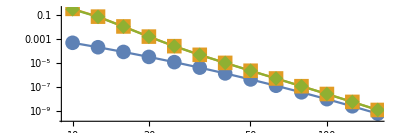

Saved as Lognormal Estimates.pdf

Times:

* Asymptotics: {0.000133744,0.0000488206,0.0000422565,0.0000422565,0.0000402052,0.0000393847,0.0000418462,0.0000393847,0.0000389744,0.0000389744,0.000203898,0.0000631796,0.0000418462}

* Polar (R=1e5): {14.79807,12.483837,12.296297,10.40615,7.2122034,1.780831,1.843318,1.843321,1.845643,1.843319,1.79786,1.827695,1.827699}

* Asmussen-Kroese (R=1e5): {40.3177932,40.3293305,41.7571443,40.534559,40.0526688,40.0926721,39.9589599,39.9426843,40.0208049,39.9530523,39.9374264,40.1093437,39.9531101}

Estimated Relative errors:

* Polar (R=1e5): {0.00487756,0.00706274,0.00934917,0.00898385,0.00825951,0.0036736,0.00250899,0.0014975,0.00125748,0.000887034,0.000757046,0.000522224,0.000425423}

* Asmussen-Kroese (R=1e5): {0.0264517,0.0172597,0.0143325,0.0104562,0.00717312,0.00327196,0.00199692,0.00149565,0.000910313,0.000665692,0.000499307,0.000391243,0.000299304}

ESTIMATED RELATIVE ERRORS PLOT

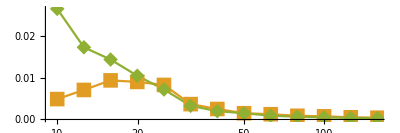

Saved as Lognormal Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Lognormal";Print[Name];
γs=10^Range[1,2.25,0.1];
d=12;
μs =-Range[d]/d;
σs=√(Range[d]/d);
𝒟=CopulaDistribution["Product",Table[LogNormalDistribution[μs[[i]],σs[[i]]],{i,d}]];
f[x_]:=IndPDF[Table[MarginalDistribution[𝒟,i],{i,d}],x];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>, AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb};
```

Test 2

Pareto

[Compare]Asymptotics

[Compare] Completed in 0.000449642 seconds.

[Compare] Asymptotics (0.0000849232 seconds): P(S > 1) estimate is 0.125

[Compare] Asymptotics (0.0000931283 seconds): P(S > 10^(1/4)) estimate is 0.0466307

[Compare] Asymptotics (0.000044718 seconds): P(S > √10) estimate is 0.0138678

[Compare] Asymptotics (0.000043077 seconds): P(S > 10^(3/4)) estimate is 0.00344155

[Compare] Asymptotics (0.0000283077 seconds): P(S > 10) estimate is 0.000751315

[Compare] Asymptotics (0.0000455385 seconds): P(S > 10 10^(1/4)) estimate is 0.00015091

[Compare] Asymptotics (0.0000397949 seconds): P(S > 10 √10) estimate is 0.000028803

[Compare] Asymptotics (0.0000443077 seconds): P(S > 10 10^(3/4)) estimate is 5.33377×10^-6

[Compare] Asymptotics (0.0000258462 seconds): P(S > 100) estimate is 9.7059×10^-7

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 1)…

Time to simulate radii: 1.13265

Time to simulate angles: 12.4681

Orig pdf time 1.10586

Angle pdf time = 19.181

Number of wasted samples = 60582(60.582%)

[PolarEstimator] P(S > 1) estimate: 0.990441. Correction: 7.92353

[PolarEstimator] Estimating P(S > 10^(1/4))…

Time to simulate radii: 1.44063

Time to simulate angles: 12.2796

Orig pdf time 1.12251

Angle pdf time = 19.1553

Number of wasted samples = 22068(22.068%)

[PolarEstimator] P(S > 10^(1/4)) estimate: 0.738323. Correction: 15.8334

[PolarEstimator] Estimating P(S > √10)…

Time to simulate radii: 1.37008

Time to simulate angles: 12.1885

Orig pdf time 1.11097

Angle pdf time = 19.671

Number of wasted samples = 2152(2.152%)

[PolarEstimator] P(S > √10) estimate: 0.171204. Correction: 12.3454

[PolarEstimator] Estimating P(S > 10^(3/4))…

Time to simulate radii: 1.4354

Time to simulate angles: 12.275

Orig pdf time 1.09705

Angle pdf time = 19.5091

Number of wasted samples = 131(0.131%)

[PolarEstimator] P(S > 10^(3/4)) estimate: 0.0150862. Correction: 4.38353

[PolarEstimator] Estimating P(S > 10)…

Time to simulate radii: 1.13934

Time to simulate angles: 12.2758

Orig pdf time 1.07771

Angle pdf time = 19.4117

Number of wasted samples = 12(0.012%)

[PolarEstimator] P(S > 10) estimate: 0.00161714. Correction: 2.15241

[PolarEstimator] Estimating P(S > 10 10^(1/4))…

Time to simulate radii: 1.46334

Time to simulate angles: 12.2545

Orig pdf time 1.13039

Angle pdf time = 19.8716

Number of wasted samples = 1(0.001%)

[PolarEstimator] P(S > 10 10^(1/4)) estimate: 0.000226643. Correction: 1.50184

[PolarEstimator] Estimating P(S > 10 √10)…

Time to simulate radii: 1.43133

Time to simulate angles: 12.1523

Orig pdf time 1.09158

Angle pdf time = 19.3675

[PolarEstimator] P(S > 10 √10) estimate: 0.000035951. Correction: 1.24817

[PolarEstimator] Estimating P(S > 10 10^(3/4))…

Time to simulate radii: 1.48781

Time to simulate angles: 12.4396

Orig pdf time 1.12821

Angle pdf time = 20.0002

[PolarEstimator] P(S > 10 10^(3/4)) estimate: 6.03232×10^-6. Correction: 1.13097

[PolarEstimator] Estimating P(S > 100)…

Time to simulate radii: 1.13744

Time to simulate angles: 12.2462

Orig pdf time 1.05867

Angle pdf time = 19.5913

[PolarEstimator] P(S > 100) estimate: 1.03982×10^-6. Correction: 1.07133

[Compare] Completed in 314.34217 seconds.

[Compare] Polar (R=1e5) (34.766885 seconds): P(S > 1) estimate is 0.990441

[Compare] Polar (R=1e5) (34.858296 seconds): P(S > 10^(1/4)) estimate is 0.738323

[Compare] Polar (R=1e5) (35.079352 seconds): P(S > √10) estimate is 0.171204

[Compare] Polar (R=1e5) (35.011892 seconds): P(S > 10^(3/4)) estimate is 0.0150862

[Compare] Polar (R=1e5) (34.441244 seconds): P(S > 10) estimate is 0.00161714

[Compare] Polar (R=1e5) (35.3973806 seconds): P(S > 10 10^(1/4)) estimate is 0.000226643

[Compare] Polar (R=1e5) (34.440917 seconds): P(S > 10 √10) estimate is 0.000035951

[Compare] Polar (R=1e5) (35.4718086 seconds): P(S > 10 10^(3/4)) estimate is 6.03232×10^-6

[Compare] Polar (R=1e5) (34.874395 seconds): P(S > 100) estimate is 1.03982×10^-6

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 1)…

(AK) Main estimation took: 48.3703

[AKEstimator] Estimating P(S > 10^(1/4))…

(AK) Main estimation took: 66.7703

[AKEstimator] Estimating P(S > √10)…

(AK) Main estimation took: 83.2139

[AKEstimator] Estimating P(S > 10^(3/4))…

(AK) Main estimation took: 59.8732

[AKEstimator] Estimating P(S > 10)…

(AK) Main estimation took: 60.496

[AKEstimator] Estimating P(S > 10 10^(1/4))…

(AK) Main estimation took: 57.6631

[AKEstimator] Estimating P(S > 10 √10)…

(AK) Main estimation took: 59.4862

[AKEstimator] Estimating P(S > 10 10^(3/4))…

(AK) Main estimation took: 57.8454

[AKEstimator] Estimating P(S > 100)…

(AK) Main estimation took: 57.1919

[Compare] Completed in 555.063175 seconds.

[Compare] Asmussen-Kroese (R=1e5) (48.9856517 seconds): P(S > 1) estimate is 0.984512

[Compare] Asmussen-Kroese (R=1e5) (67.1438155 seconds): P(S > 10^(1/4)) estimate is 0.722903

[Compare] Asmussen-Kroese (R=1e5) (83.6917912 seconds): P(S > √10) estimate is 0.170808

[Compare] Asmussen-Kroese (R=1e5) (60.3337896 seconds): P(S > 10^(3/4)) estimate is 0.0151006

[Compare] Asmussen-Kroese (R=1e5) (60.9496241 seconds): P(S > 10) estimate is 0.00161627

[Compare] Asmussen-Kroese (R=1e5) (58.0960645 seconds): P(S > 10 10^(1/4)) estimate is 0.000226646

[Compare] Asmussen-Kroese (R=1e5) (59.9151417 seconds): P(S > 10 √10) estimate is 0.0000359622

[Compare] Asmussen-Kroese (R=1e5) (58.3370699 seconds): P(S > 10 10^(3/4)) estimate is 6.03207×10^-6

[Compare] Asmussen-Kroese (R=1e5) (57.6102272 seconds): P(S > 100) estimate is 1.03966×10^-6

Estimates:

* Asymptotics: {0.125,0.0466307,0.0138678,0.00344155,0.000751315,0.00015091,0.000028803,5.33377×10^-6,9.7059×10^-7}

* Polar (R=1e5): {0.990441,0.738323,0.171204,0.0150862,0.00161714,0.000226643,0.000035951,6.03232×10^-6,1.03982×10^-6}

* Asmussen-Kroese (R=1e5): {0.984512,0.722903,0.170808,0.0151006,0.00161627,0.000226646,0.0000359622,6.03207×10^-6,1.03966×10^-6}

ESTIMATES PLOT

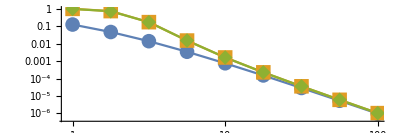

Saved as Pareto Estimates.pdf

Times:

* Asymptotics: {0.0000849232,0.0000931283,0.000044718,0.000043077,0.0000283077,0.0000455385,0.0000397949,0.0000443077,0.0000258462}

* Polar (R=1e5): {34.766885,34.858296,35.079352,35.011892,34.441244,35.3973806,34.440917,35.4718086,34.874395}

* Asmussen-Kroese (R=1e5): {48.9856517,67.1438155,83.6917912,60.3337896,60.9496241,58.0960645,59.9151417,58.3370699,57.6102272}

Estimated Relative errors:

* Polar (R=1e5): {0.00579522,0.00371656,0.00460075,0.00430104,0.00205515,0.000870479,0.000416432,0.000256925,0.000140132}

* Asmussen-Kroese (R=1e5): {0.0162179,0.0199898,0.0111782,0.00396655,0.00161228,0.000718746,0.000289926,0.000139586,0.0000732772}

ESTIMATED RELATIVE ERRORS PLOT

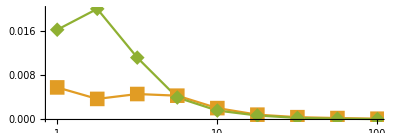

Saved as Pareto Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Pareto";Print[Name];
γs=10^Range[0,2,1/4];
d=16;
𝒟=CopulaDistribution["Product",
Table[ParetoDistribution[1,2+i,0],{i,d}]];
f[x_]:=IndPDF[Table[MarginalDistribution[𝒟,i],{i,d}],x];

(* Note:Mathematica doesn't like TruncatedDistribution with Paretos. So we avoid the built-in truncation method here. *)
RandomRadiusTrunc[γ_,R_]:=SimulateTruncated[MarginalDistribution[𝒟,1],γ,R];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User","𝒟Angles"-> SubexpIndSetup[𝒟],"c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,1],WorkingPrecision-> 50,"R"->R,"SimulateTruncRadius"-> RandomRadiusTrunc|>, AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName->Name,Verbosity-> Verb}
```

Test 3

Weibull Heavy

[Compare]Asymptotics

[Compare] Completed in 0.000584616 seconds.

[Compare] Asymptotics (0.000140718 seconds): P(S > 10) estimate is 0.168929

[Compare] Asymptotics (0.000103795 seconds): P(S > 10 10^(1/3)) estimate is 0.115969

[Compare] Asymptotics (0.0000697437 seconds): P(S > 10 10^(2/3)) estimate is 0.073523

[Compare] Asymptotics (0.0000348718 seconds): P(S > 100) estimate is 0.0423292

[Compare] Asymptotics (0.000046359 seconds): P(S > 100 10^(1/3)) estimate is 0.0216839

[Compare] Asymptotics (0.0000443077 seconds): P(S > 100 10^(2/3)) estimate is 0.00964237

[Compare] Asymptotics (0.0000344616 seconds): P(S > 1000) estimate is 0.00361229

[Compare] Asymptotics (0.0000480001 seconds): P(S > 1000 10^(1/3)) estimate is 0.00109948

[Compare] Asymptotics (0.0000426667 seconds): P(S > 1000 10^(2/3)) estimate is 0.000260205

[Compare] Asymptotics (0.0000196923 seconds): P(S > 10000) estimate is 0.0000453999

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10)…

Time to simulate radii: 1.47638

Time to simulate angles: 13.3205

Angle pdf time = 31.1788

The rest time 1.05507

Number of wasted samples = 44514(44.514%)

[PolarEstimator] P(S > 10) estimate: 0.672317. Correction: 3.97989

[PolarEstimator] Estimating P(S > 10 10^(1/3))…

Time to simulate radii: 1.51582

Time to simulate angles: 12.4122

Angle pdf time = 32.5866

g_S[Ss] time = 1.06921

Number of wasted samples = 32231(32.231%)

[PolarEstimator] P(S > 10 10^(1/3)) estimate: 0.547193. Correction: 4.71845

[PolarEstimator] Estimating P(S > 10 10^(2/3))…

Time to simulate radii: 1.50277

Time to simulate angles: 12.9943

Angle pdf time = 33.0434

Number of wasted samples = 20475(20.475%)

[PolarEstimator] P(S > 10 10^(2/3)) estimate: 0.387756. Correction: 5.27395

[PolarEstimator] Estimating P(S > 100)…

Time to simulate radii: 1.92926

Time to simulate angles: 12.5106

Angle pdf time = 31.4063

g_S[Ss] time = 1.12622

Number of wasted samples = 11452(11.452%)

[PolarEstimator] P(S > 100) estimate: 0.230927. Correction: 5.45549

[PolarEstimator] Estimating P(S > 100 10^(1/3))…

Time to simulate radii: 1.508

Time to simulate angles: 12.2111

Angle pdf time = 31.9315

g_S[Ss] time = 1.06183

Number of wasted samples = 5414(5.414%)

[PolarEstimator] P(S > 100 10^(1/3)) estimate: 0.1146. Correction: 5.28502

[PolarEstimator] Estimating P(S > 100 10^(2/3))…

Time to simulate radii: 1.59557

Time to simulate angles: 12.369

Orig pdf time 1.00428

Angle pdf time = 34.4322

Number of wasted samples = 2130(2.13%)

[PolarEstimator] P(S > 100 10^(2/3)) estimate: 0.0465548. Correction: 4.82815

[PolarEstimator] Estimating P(S > 1000)…

Time to simulate radii: 1.54965

Time to simulate angles: 12.5946

Angle pdf time = 30.7016

Number of wasted samples = 715(0.715%)

[PolarEstimator] P(S > 1000) estimate: 0.015396. Correction: 4.2621

[PolarEstimator] Estimating P(S > 1000 10^(1/3))…

Time to simulate radii: 1.51416

Time to simulate angles: 11.2517

Angle pdf time = 28.7014

Number of wasted samples = 159(0.159%)

[PolarEstimator] P(S > 1000 10^(1/3)) estimate: 0.00409217. Correction: 3.72193

[PolarEstimator] Estimating P(S > 1000 10^(2/3))…

Time to simulate radii: 1.5088

Time to simulate angles: 13.2481

Orig pdf time 1.19048

Angle pdf time = 32.652

g_S[Ss] time = 1.49889

Number of wasted samples = 37(0.037%)

[PolarEstimator] P(S > 1000 10^(2/3)) estimate: 0.000842654. Correction: 3.23843

[PolarEstimator] Estimating P(S > 10000)…

Time to simulate radii: 1.98108

Time to simulate angles: 17.1877

Angle pdf time = 30.0807

g_S[Ss] time = 1.26

Number of wasted samples = 6(0.006%)

[PolarEstimator] P(S > 10000) estimate: 0.000128982. Correction: 2.84103

[Compare] Completed in 489.852329 seconds.

[Compare] Polar (R=1e5) (49.0342282 seconds): P(S > 10) estimate is 0.672317

[Compare] Polar (R=1e5) (49.4100296 seconds): P(S > 10 10^(1/3)) estimate is 0.547193

[Compare] Polar (R=1e5) (50.2133923 seconds): P(S > 10 10^(2/3)) estimate is 0.387756

[Compare] Polar (R=1e5) (48.5776581 seconds): P(S > 100) estimate is 0.230927

[Compare] Polar (R=1e5) (48.279856 seconds): P(S > 100 10^(1/3)) estimate is 0.1146

[Compare] Polar (R=1e5) (50.7995107 seconds): P(S > 100 10^(2/3)) estimate is 0.0465548

[Compare] Polar (R=1e5) (47.0684739 seconds): P(S > 1000) estimate is 0.015396

[Compare] Polar (R=1e5) (43.7391455 seconds): P(S > 1000 10^(1/3)) estimate is 0.00409217

[Compare] Polar (R=1e5) (50.7078401 seconds): P(S > 1000 10^(2/3)) estimate is 0.000842654

[Compare] Polar (R=1e5) (52.0221949 seconds): P(S > 10000) estimate is 0.000128982

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10)…

(AK) Main estimation took: 34.364

[AKEstimator] Estimating P(S > 10 10^(1/3))…

(AK) Main estimation took: 41.458

[AKEstimator] Estimating P(S > 10 10^(2/3))…

(AK) Main estimation took: 39.7338

[AKEstimator] Estimating P(S > 100)…

(AK) Main estimation took: 43.237

[AKEstimator] Estimating P(S > 100 10^(1/3))…

(AK) Main estimation took: 37.9338

[AKEstimator] Estimating P(S > 100 10^(2/3))…

(AK) Main estimation took: 38.1466

[AKEstimator] Estimating P(S > 1000)…

(AK) Main estimation took: 44.4653

[AKEstimator] Estimating P(S > 1000 10^(1/3))…

(AK) Main estimation took: 36.6319

[AKEstimator] Estimating P(S > 1000 10^(2/3))…

(AK) Main estimation took: 40.0343

[AKEstimator] Estimating P(S > 10000)…

(AK) Main estimation took: 48.1433

[Compare] Completed in 404.935837 seconds.

[Compare] Asmussen-Kroese (R=1e5) (34.453832 seconds): P(S > 10) estimate is 0.72864

[Compare] Asmussen-Kroese (R=1e5) (41.579355 seconds): P(S > 10 10^(1/3)) estimate is 0.567627

[Compare] Asmussen-Kroese (R=1e5) (39.8155021 seconds): P(S > 10 10^(2/3)) estimate is 0.385622

[Compare] Asmussen-Kroese (R=1e5) (43.3105739 seconds): P(S > 100) estimate is 0.224608

[Compare] Asmussen-Kroese (R=1e5) (38.009413 seconds): P(S > 100 10^(1/3)) estimate is 0.109915

[Compare] Asmussen-Kroese (R=1e5) (38.2129688 seconds): P(S > 100 10^(2/3)) estimate is 0.0445046

[Compare] Asmussen-Kroese (R=1e5) (44.5331034 seconds): P(S > 1000) estimate is 0.0147723

[Compare] Asmussen-Kroese (R=1e5) (36.6997403 seconds): P(S > 1000 10^(1/3)) estimate is 0.00394333

[Compare] Asmussen-Kroese (R=1e5) (40.1024211 seconds): P(S > 1000 10^(2/3)) estimate is 0.000818256

[Compare] Asmussen-Kroese (R=1e5) (48.2189279 seconds): P(S > 10000) estimate is 0.000126112

Estimates:

* Asymptotics: {0.168929,0.115969,0.073523,0.0423292,0.0216839,0.00964237,0.00361229,0.00109948,0.000260205,0.0000453999}

* Polar (R=1e5): {0.672317,0.547193,0.387756,0.230927,0.1146,0.0465548,0.015396,0.00409217,0.000842654,0.000128982}

* Asmussen-Kroese (R=1e5): {0.72864,0.567627,0.385622,0.224608,0.109915,0.0445046,0.0147723,0.00394333,0.000818256,0.000126112}

ESTIMATES PLOT

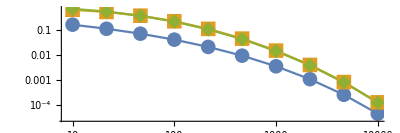

Saved as Weibull Heavy Estimates.pdf

Times:

* Asymptotics: {0.000140718,0.000103795,0.0000697437,0.0000348718,0.000046359,0.0000443077,0.0000344616,0.0000480001,0.0000426667,0.0000196923}

* Polar (R=1e5): {49.0342282,49.4100296,50.2133923,48.5776581,48.279856,50.7995107,47.0684739,43.7391455,50.7078401,52.0221949}

* Asmussen-Kroese (R=1e5): {34.453832,41.579355,39.8155021,43.3105739,38.009413,38.2129688,44.5331034,36.6997403,40.1024211,48.2189279}

Estimated Relative errors:

* Polar (R=1e5): {0.00296302,0.00234406,0.00183256,0.00146146,0.0012197,0.0010641,0.000943972,0.000818123,0.000654951,0.000481899}

* Asmussen-Kroese (R=1e5): {0.00191439,0.00160024,0.00132092,0.00111371,0.000961756,0.00086649,0.00078531,0.000664148,0.000516609,0.000375127}

ESTIMATED RELATIVE ERRORS PLOT

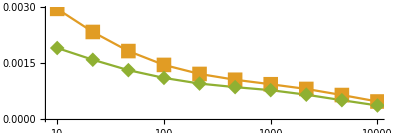

Saved as Weibull Heavy Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Weibull Heavy";Print[Name];
γs=10^Range[1+2/3,6,1/2];
d=8;
𝒟=CopulaDistribution["Product",Table[WeibullDistribution[1/4,i/d],{i,d}]];
f[x_]:=IndPDF[Table[MarginalDistribution[𝒟,i],{i,d}],x];

RandomRadiusTrunc[γ_,R_]:=SimulateTruncated[MarginalDistribution[𝒟,1],γ,R];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],"SimulateTruncRadius"-> RandomRadiusTrunc,
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>,AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb}
```

Test 4

Weibull Light

[Compare]Asymptotics

[Compare] Completed in 0.150854 seconds.

[Compare] Asymptotics (0.0147857 seconds): P(S > 10) estimate is 1.

[Compare] Asymptotics (0.0142728 seconds): P(S > 11) estimate is 0.366451

[Compare] Asymptotics (0.0147504 seconds): P(S > 12) estimate is 0.0803961

[Compare] Asymptotics (0.0134406 seconds): P(S > 13) estimate is 0.0135631

[Compare] Asymptotics (0.0134786 seconds): P(S > 14) estimate is 0.00177593

[Compare] Asymptotics (0.0130732 seconds): P(S > 15) estimate is 0.000181819

[Compare] Asymptotics (0.0134355 seconds): P(S > 16) estimate is 0.0000146415

[Compare] Asymptotics (0.013334 seconds): P(S > 17) estimate is 9.3191×10^-7

[Compare] Asymptotics (0.0134361 seconds): P(S > 18) estimate is 4.70712×10^-8

[Compare] Asymptotics (0.0132912 seconds): P(S > 19) estimate is 1.8932×10^-9

[Compare] Asymptotics (0.0135557 seconds): P(S > 20) estimate is 6.08044×10^-11

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10)…

Time to simulate radii: 50.5024

Angle pdf time = 556.74

[PolarEstimator] P(S > 10) estimate: 0.177558. Correction: 0.177558

[PolarEstimator] Estimating P(S > 11)…

Time to simulate radii: 50.4803

Angle pdf time = 593.791

[PolarEstimator] P(S > 11) estimate: 0.0771016. Correction: 0.210401

[PolarEstimator] Estimating P(S > 12)…

Time to simulate radii: 58.5911

Angle pdf time = 690.366

[PolarEstimator] P(S > 12) estimate: 0.0206327. Correction: 0.256638

[PolarEstimator] Estimating P(S > 13)…

Time to simulate radii: 57.1089

Angle pdf time = 592.715

[PolarEstimator] P(S > 13) estimate: 0.00414413. Correction: 0.305545

[PolarEstimator] Estimating P(S > 14)…

Time to simulate radii: 60.4166

Angle pdf time = 601.156

[PolarEstimator] P(S > 14) estimate: 0.000629688. Correction: 0.354569

[PolarEstimator] Estimating P(S > 15)…

Time to simulate radii: 63.8659

Angle pdf time = 564.605

[PolarEstimator] P(S > 15) estimate: 0.0000734049. Correction: 0.403725

[PolarEstimator] Estimating P(S > 16)…

Time to simulate radii: 67.1463

Angle pdf time = 568.001

[PolarEstimator] P(S > 16) estimate: 6.56955×10^-6. Correction: 0.448694

[PolarEstimator] Estimating P(S > 17)…

Time to simulate radii: 69.9398

Angle pdf time = 618.595

[PolarEstimator] P(S > 17) estimate: 4.4927×10^-7. Correction: 0.482095

[PolarEstimator] Estimating P(S > 18)…

Time to simulate radii: 74.9159

Angle pdf time = 604.322

[PolarEstimator] P(S > 18) estimate: 2.30888×10^-8. Correction: 0.490508

[PolarEstimator] Estimating P(S > 19)…

Time to simulate radii: 73.8184

Angle pdf time = 580.369

[PolarEstimator] P(S > 19) estimate: 9.42832×10^-10. Correction: 0.49801

[PolarEstimator] Estimating P(S > 20)…

Time to simulate radii: 72.1614

Angle pdf time = 567.263

[PolarEstimator] P(S > 20) estimate: 3.01911×10^-11. Correction: 0.496528

[Compare] Completed in 7240.45013 seconds.

[Compare] Polar (R=1e5) (607.6617563 seconds): P(S > 10) estimate is 0.177558

[Compare] Polar (R=1e5) (644.7148755 seconds): P(S > 11) estimate is 0.0771016

[Compare] Polar (R=1e5) (749.2798564 seconds): P(S > 12) estimate is 0.0206327

[Compare] Polar (R=1e5) (650.1521866 seconds): P(S > 13) estimate is 0.00414413

[Compare] Polar (R=1e5) (661.8578561 seconds): P(S > 14) estimate is 0.000629688

[Compare] Polar (R=1e5) (628.7649633 seconds): P(S > 15) estimate is 0.0000734049

[Compare] Polar (R=1e5) (635.439345 seconds): P(S > 16) estimate is 6.56955×10^-6

[Compare] Polar (R=1e5) (688.8263987 seconds): P(S > 17) estimate is 4.4927×10^-7

[Compare] Polar (R=1e5) (679.5448677 seconds): P(S > 18) estimate is 2.30888×10^-8

[Compare] Polar (R=1e5) (654.4814342 seconds): P(S > 19) estimate is 9.42832×10^-10

[Compare] Polar (R=1e5) (639.7265903 seconds): P(S > 20) estimate is 3.01911×10^-11

[Compare]Exponential tilting (R=1e5)

[Compare] Completed in 4842.300964 seconds.

[Compare] Exponential tilting (R=1e5) (559.9170254 seconds): P(S > 10) estimate is 0.212387

[Compare] Exponential tilting (R=1e5) (521.2928163 seconds): P(S > 11) estimate is 0.0772693

[Compare] Exponential tilting (R=1e5) (487.8479033 seconds): P(S > 12) estimate is 0.0205746

[Compare] Exponential tilting (R=1e5) (458.5392269 seconds): P(S > 13) estimate is 0.0041482

[Compare] Exponential tilting (R=1e5) (443.0823429 seconds): P(S > 14) estimate is 0.000630442

[Compare] Exponential tilting (R=1e5) (423.9142465 seconds): P(S > 15) estimate is 0.0000726332

[Compare] Exponential tilting (R=1e5) (404.936161 seconds): P(S > 16) estimate is 6.74119×10^-6

[Compare] Exponential tilting (R=1e5) (387.1091414 seconds): P(S > 17) estimate is 4.6499×10^-7

[Compare] Exponential tilting (R=1e5) (384.637 seconds): P(S > 18) estimate is 2.50346×10^-8

[Compare] Exponential tilting (R=1e5) (403.677089 seconds): P(S > 19) estimate is 1.08746×10^-9

[Compare] Exponential tilting (R=1e5) (367.3480111 seconds): P(S > 20) estimate is 3.68746×10^-11

Estimates:

* Asymptotics: {1.,0.366451,0.0803961,0.0135631,0.00177593,0.000181819,0.0000146415,9.3191×10^-7,4.70712×10^-8,1.8932×10^-9,6.08044×10^-11}

* Polar (R=1e5): {0.177558,0.0771016,0.0206327,0.00414413,0.000629688,0.0000734049,6.56955×10^-6,4.4927×10^-7,2.30888×10^-8,9.42832×10^-10,3.01911×10^-11}

* Exponential tilting (R=1e5): {0.212387,0.0772693,0.0205746,0.0041482,0.000630442,0.0000726332,6.74119×10^-6,4.6499×10^-7,2.50346×10^-8,1.08746×10^-9,3.68746×10^-11}

ESTIMATES PLOT

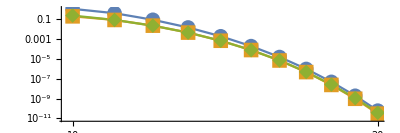

Saved as Weibull Light Estimates.pdf

Times:

* Asymptotics: {0.0147857,0.0142728,0.0147504,0.0134406,0.0134786,0.0130732,0.0134355,0.013334,0.0134361,0.0132912,0.0135557}

* Polar (R=1e5): {607.6617563,644.7148755,749.2798564,650.1521866,661.8578561,628.7649633,635.439345,688.8263987,679.5448677,654.4814342,639.7265903}

* Exponential tilting (R=1e5): {559.9170254,521.2928163,487.8479033,458.5392269,443.0823429,423.9142465,404.936161,387.1091414,384.637,403.677089,367.3480111}

Estimated Relative errors:

* Polar (R=1e5): {0.00236677,0.00223979,0.00235527,0.00258439,0.00331173,0.00309948,0.0035355,0.00413226,0.00407959,0.00389514,0.003792}

* Exponential tilting (R=1e5): {0.0164061,0.0154997,0.0148564,0.0141186,0.0136744,0.0133586,0.0130358,0.0129056,0.0128094,0.0128165,0.0127773}

ESTIMATED RELATIVE ERRORS PLOT

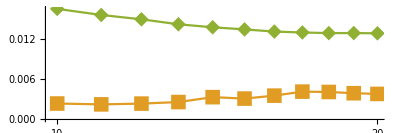

Saved as Weibull Light Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Weibull Light"; Print[Name];
d=10;β=2;
γs=Range[10,20,1];
𝒟=ProductDistribution @@ ConstantArray[WeibullDistribution[β,1],d];
f[x_]:=IndPDF[Table[MarginalDistribution[𝒟,i],{i,d}],x];

Subscript[𝒟G, S]=WeibullSumDistribution[d,β];
RandomRadiusTrunc[γ_,R_]:=SimulateTruncatedWeibull[Subscript[𝒟G, S],d,β,γ,R]
CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User","𝒟Angles"->WeibullAngleSetup[𝒟],"SimulateTruncRadius"-> RandomRadiusTrunc, "c_S"->1,"𝒟G_S"-> Subscript[𝒟G, S],"SymmAngle"-> True,"R"->R|>,ExpTiltArgs-><|"𝒟"-> 𝒟,"R"->R,"TiltProp"-> WeibullTiltedProposals|>, TestName-> Name,Verbosity-> Verb};
```

Test 5

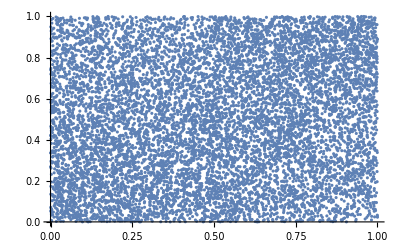

```mathematica
ListPlot[RandomVariate[CopulaDistribution[{"Frank",1/2},{UniformDistribution[],UniformDistribution[]}],10^4]]
```

Lognormal Frank

[Compare]Asymptotics

[Compare] Completed in 0.00195427 seconds.

[Compare] Asymptotics (0.000274362 seconds): P(S > 10.) estimate is 0.00047899

[Compare] Asymptotics (0.000152992 seconds): P(S > 12.5893) estimate is 0.000205558

[Compare] Asymptotics (0.000140343 seconds): P(S > 15.8489) estimate is 0.0000839093

[Compare] Asymptotics (0.00013944 seconds): P(S > 19.9526) estimate is 0.0000325717

[Compare] Asymptotics (0.000141849 seconds): P(S > 25.1189) estimate is 0.0000120205

[Compare] Asymptotics (0.000143656 seconds): P(S > 31.6228) estimate is 4.21666×10^-6

[Compare] Asymptotics (0.000131609 seconds): P(S > 39.8107) estimate is 1.40572×10^-6

[Compare] Asymptotics (0.000128598 seconds): P(S > 50.1187) estimate is 4.45286×10^-7

[Compare] Asymptotics (0.000129803 seconds): P(S > 63.0957) estimate is 1.34008×10^-7

[Compare] Asymptotics (0.000129803 seconds): P(S > 79.4328) estimate is 3.83101×10^-8

[Compare] Asymptotics (0.000130405 seconds): P(S > 100.) estimate is 1.04025×10^-8

[Compare] Asymptotics (0.000171966 seconds): P(S > 125.893) estimate is 2.68262×10^-9

[Compare] Asymptotics (0.00013944 seconds): P(S > 158.489) estimate is 6.56953×10^-10

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10.)…

Time to simulate angles: 12.7768

Orig pdf time 50.0884

Angle pdf time = 25.8134

Number of wasted samples = 7142(7.142%)

[PolarEstimator] P(S > 10.) estimate: 0.311243. Correction: 649.79

[PolarEstimator] Estimating P(S > 12.5893)…

Time to simulate angles: 12.5007

Orig pdf time 49.4774

Angle pdf time = 26.2899

Number of wasted samples = 1253(1.253%)

[PolarEstimator] P(S > 12.5893) estimate: 0.10971. Correction: 533.717

[PolarEstimator] Estimating P(S > 15.8489)…

Time to simulate angles: 12.282

Orig pdf time 42.7481

Angle pdf time = 22.9828

Number of wasted samples = 197(0.197%)

[PolarEstimator] P(S > 15.8489) estimate: 0.0328941. Correction: 392.02

[PolarEstimator] Estimating P(S > 19.9526)…

Time to simulate angles: 12.308

Orig pdf time 33.2579

Angle pdf time = 19.4325

Number of wasted samples = 28(0.028%)

[PolarEstimator] P(S > 19.9526) estimate: 0.00396981. Correction: 121.879

[PolarEstimator] Estimating P(S > 25.1189)…

Time to simulate angles: 12.2309

Orig pdf time 26.7153

Angle pdf time = 16.51

Number of wasted samples = 5(0.005%)

[PolarEstimator] P(S > 25.1189) estimate: 0.000495634. Correction: 41.2324

[PolarEstimator] Estimating P(S > 31.6228)…

Time to simulate angles: 12.1869

Orig pdf time 15.1817

Angle pdf time = 11.7071

[PolarEstimator] P(S > 31.6228) estimate: 0.0000891408. Correction: 21.1402

[PolarEstimator] Estimating P(S > 39.8107)…

Time to simulate angles: 12.3187

Orig pdf time 26.7156

Angle pdf time = 16.5315

Number of wasted samples = 2(0.002%)

[PolarEstimator] P(S > 39.8107) estimate: 0.0000171017. Correction: 12.1659

[PolarEstimator] Estimating P(S > 50.1187)…

Time to simulate angles: 12.3266

Orig pdf time 15.1405

Angle pdf time = 11.7327

[PolarEstimator] P(S > 50.1187) estimate: 2.85577×10^-6. Correction: 6.41333

[PolarEstimator] Estimating P(S > 63.0957)…

Time to simulate angles: 12.3123

Orig pdf time 15.2507

Angle pdf time = 11.8139

[PolarEstimator] P(S > 63.0957) estimate: 6.18297×10^-7. Correction: 4.61389

[PolarEstimator] Estimating P(S > 79.4328)…

Time to simulate angles: 12.3758

Orig pdf time 15.297

Angle pdf time = 11.8359

[PolarEstimator] P(S > 79.4328) estimate: 1.3184×10^-7. Correction: 3.44139

[PolarEstimator] Estimating P(S > 100.)…

Time to simulate angles: 12.4403

Orig pdf time 15.3266

Angle pdf time = 11.8435

[PolarEstimator] P(S > 100.) estimate: 3.20443×10^-8. Correction: 3.08044

[PolarEstimator] Estimating P(S > 125.893)…

Time to simulate angles: 12.2862

Orig pdf time 15.1899

Angle pdf time = 11.7538

[PolarEstimator] P(S > 125.893) estimate: 6.53718×10^-9. Correction: 2.43686

[PolarEstimator] Estimating P(S > 158.489)…

Time to simulate angles: 12.372

Orig pdf time 15.9845

Angle pdf time = 12.2417

[PolarEstimator] P(S > 158.489) estimate: 1.43038×10^-9. Correction: 2.17729

[Compare] Completed in 709.263568 seconds.

[Compare] Polar (R=1e5) (88.9450874 seconds): P(S > 10.) estimate is 0.311243

[Compare] Polar (R=1e5) (88.4750605 seconds): P(S > 12.5893) estimate is 0.10971

[Compare] Polar (R=1e5) (78.2434752 seconds): P(S > 15.8489) estimate is 0.0328941

[Compare] Polar (R=1e5) (65.2507321 seconds): P(S > 19.9526) estimate is 0.00396981

[Compare] Polar (R=1e5) (55.6891853 seconds): P(S > 25.1189) estimate is 0.000495634

[Compare] Polar (R=1e5) (39.1052367 seconds): P(S > 31.6228) estimate is 0.0000891408

[Compare] Polar (R=1e5) (55.8101921 seconds): P(S > 39.8107) estimate is 0.0000171017

[Compare] Polar (R=1e5) (39.2372443 seconds): P(S > 50.1187) estimate is 2.85577×10^-6

[Compare] Polar (R=1e5) (39.4072539 seconds): P(S > 63.0957) estimate is 6.18297×10^-7

[Compare] Polar (R=1e5) (39.5342613 seconds): P(S > 79.4328) estimate is 1.3184×10^-7

[Compare] Polar (R=1e5) (39.635267 seconds): P(S > 100.) estimate is 3.20443×10^-8

[Compare] Polar (R=1e5) (39.2832469 seconds): P(S > 125.893) estimate is 6.53718×10^-9

[Compare] Polar (R=1e5) (40.6473249 seconds): P(S > 158.489) estimate is 1.43038×10^-9

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10.)…

(AK) Simulating took: 154.181

(AK) Main estimation took: 618.678

[AKEstimator] Estimating P(S > 12.5893)…

(AK) Simulating took: 153.565

(AK) Main estimation took: 610.871

[AKEstimator] Estimating P(S > 15.8489)…

(AK) Simulating took: 152.94

(AK) Main estimation took: 612.047

[AKEstimator] Estimating P(S > 19.9526)…

(AK) Simulating took: 154.103

(AK) Main estimation took: 619.256

[AKEstimator] Estimating P(S > 25.1189)…

(AK) Simulating took: 153.763

(AK) Main estimation took: 630.799

[AKEstimator] Estimating P(S > 31.6228)…

(AK) Simulating took: 157.315

(AK) Main estimation took: 615.521

[AKEstimator] Estimating P(S > 39.8107)…

(AK) Simulating took: 153.069

(AK) Main estimation took: 618.697

[AKEstimator] Estimating P(S > 50.1187)…

(AK) Simulating took: 159.127

(AK) Main estimation took: 625.914

[AKEstimator] Estimating P(S > 63.0957)…

(AK) Simulating took: 153.377

(AK) Main estimation took: 615.814

[AKEstimator] Estimating P(S > 79.4328)…

(AK) Simulating took: 155.918

(AK) Main estimation took: 624.15

[AKEstimator] Estimating P(S > 100.)…

(AK) Simulating took: 154.091

(AK) Main estimation took: 617.643

[AKEstimator] Estimating P(S > 125.893)…

(AK) Simulating took: 157.348

(AK) Main estimation took: 622.48

[AKEstimator] Estimating P(S > 158.489)…

(AK) Simulating took: 155.412

(AK) Main estimation took: 620.093

[Compare] Completed in 10066.65378 seconds.

[Compare] Asmussen-Kroese (R=1e5) (772.8952071 seconds): P(S > 10.) estimate is 0.309293

[Compare] Asmussen-Kroese (R=1e5) (764.4747255 seconds): P(S > 12.5893) estimate is 0.117458

[Compare] Asmussen-Kroese (R=1e5) (765.025757 seconds): P(S > 15.8489) estimate is 0.0301548

[Compare] Asmussen-Kroese (R=1e5) (773.3962357 seconds): P(S > 19.9526) estimate is 0.00702913

[Compare] Asmussen-Kroese (R=1e5) (784.5998766 seconds): P(S > 25.1189) estimate is 0.000680304

[Compare] Asmussen-Kroese (R=1e5) (772.8712057 seconds): P(S > 31.6228) estimate is 0.0000838348

[Compare] Asmussen-Kroese (R=1e5) (771.8041446 seconds): P(S > 39.8107) estimate is 0.0000146337

[Compare] Asmussen-Kroese (R=1e5) (785.0779039 seconds): P(S > 50.1187) estimate is 2.95724×10^-6

[Compare] Asmussen-Kroese (R=1e5) (769.2249972 seconds): P(S > 63.0957) estimate is 6.28477×10^-7

[Compare] Asmussen-Kroese (R=1e5) (780.1066195 seconds): P(S > 79.4328) estimate is 1.38025×10^-7

[Compare] Asmussen-Kroese (R=1e5) (771.7701428 seconds): P(S > 100.) estimate is 3.0444×10^-8

[Compare] Asmussen-Kroese (R=1e5) (779.8646057 seconds): P(S > 125.893) estimate is 6.59264×10^-9

[Compare] Asmussen-Kroese (R=1e5) (775.5423584 seconds): P(S > 158.489) estimate is 1.40614×10^-9

Estimates:

* Asymptotics: {0.00047899,0.000205558,0.0000839093,0.0000325717,0.0000120205,4.21666×10^-6,1.40572×10^-6,4.45286×10^-7,1.34008×10^-7,3.83101×10^-8,1.04025×10^-8,2.68262×10^-9,6.56953×10^-10}

* Polar (R=1e5): {0.311243,0.10971,0.0328941,0.00396981,0.000495634,0.0000891408,0.0000171017,2.85577×10^-6,6.18297×10^-7,1.3184×10^-7,3.20443×10^-8,6.53718×10^-9,1.43038×10^-9}

* Asmussen-Kroese (R=1e5): {0.309293,0.117458,0.0301548,0.00702913,0.000680304,0.0000838348,0.0000146337,2.95724×10^-6,6.28477×10^-7,1.38025×10^-7,3.0444×10^-8,6.59264×10^-9,1.40614×10^-9}

ESTIMATES PLOT

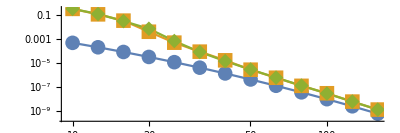

Saved as Lognormal Frank Estimates.pdf

Times:

* Asymptotics: {0.000274362,0.000152992,0.000140343,0.00013944,0.000141849,0.000143656,0.000131609,0.000128598,0.000129803,0.000129803,0.000130405,0.000171966,0.00013944}

* Polar (R=1e5): {88.9450874,88.4750605,78.2434752,65.2507321,55.6891853,39.1052367,55.8101921,39.2372443,39.4072539,39.5342613,39.635267,39.2832469,40.6473249}

* Asmussen-Kroese (R=1e5): {772.8952071,764.4747255,765.025757,773.3962357,784.5998766,772.8712057,771.8041446,785.0779039,769.2249972,780.1066195,771.7701428,779.8646057,775.5423584}

Estimated Relative errors:

* Polar (R=1e5): {0.0320927,0.0467243,0.214291,0.125425,0.158207,0.195189,0.157184,0.0400073,0.033788,0.0195306,0.0563347,0.0218581,0.0330983}

* Asmussen-Kroese (R=1e5): {0.0567139,0.0378452,0.0371517,0.26092,0.0569091,0.0138313,0.00996949,0.00783396,0.00408815,0.00323252,0.00282077,0.00251915,0.00232793}

ESTIMATED RELATIVE ERRORS PLOT

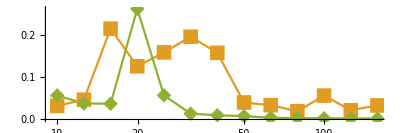

Saved as Lognormal Frank Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Lognormal Frank";Print[Name];
γs=10^Range[1,2.25,0.1];
d=12;
μs =-Range[d]/d;
σs=√(Range[d]/d);

Copula={"Frank",1/2};
Margs=Table[LogNormalDistribution[μs[[i]],σs[[i]]],{i,d}];
𝒟=CopulaDistribution[Copula,Margs];
f[x_]:=CopPDF[Copula,Margs,x]

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>, AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb};
```

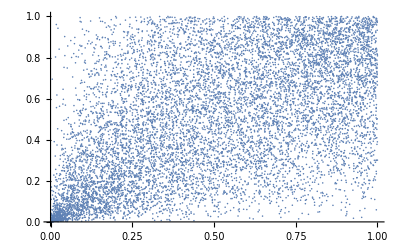

```mathematica
ListPlot[RandomVariate[CopulaDistribution[{"Clayton",0.9},{UniformDistribution[],UniformDistribution[]}],10^4]]
```

Lognormal Clayton

[Compare]Asymptotics

[Compare] Completed in 0.00218618 seconds.

[Compare] Asymptotics (0.000274665 seconds): P(S > 10.) estimate is 0.00047899

[Compare] Asymptotics (0.000187326 seconds): P(S > 12.5893) estimate is 0.000205558

[Compare] Asymptotics (0.000185519 seconds): P(S > 15.8489) estimate is 0.0000839093

[Compare] Asymptotics (0.000169859 seconds): P(S > 19.9526) estimate is 0.0000325717

[Compare] Asymptotics (0.000166847 seconds): P(S > 25.1189) estimate is 0.0000120205

[Compare] Asymptotics (0.000154499 seconds): P(S > 31.6228) estimate is 4.21666×10^-6

[Compare] Asymptotics (0.000149078 seconds): P(S > 39.8107) estimate is 1.40572×10^-6

[Compare] Asymptotics (0.000167148 seconds): P(S > 50.1187) estimate is 4.45286×10^-7

[Compare] Asymptotics (0.000173473 seconds): P(S > 63.0957) estimate is 1.34008×10^-7

[Compare] Asymptotics (0.000140946 seconds): P(S > 79.4328) estimate is 3.83101×10^-8

[Compare] Asymptotics (0.000138537 seconds): P(S > 100.) estimate is 1.04025×10^-8

[Compare] Asymptotics (0.000137634 seconds): P(S > 125.893) estimate is 2.68262×10^-9

[Compare] Asymptotics (0.000140645 seconds): P(S > 158.489) estimate is 6.56953×10^-10

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10.)…

Time to simulate angles: 8.6343

Orig pdf time 11.6939

Angle pdf time = 13.7692

Number of wasted samples = 541(0.541%)

[PolarEstimator] P(S > 10.) estimate: 0.103719. Correction: 216.536

[PolarEstimator] Estimating P(S > 12.5893)…

Time to simulate angles: 8.37698

Orig pdf time 11.347

Angle pdf time = 13.0539

Number of wasted samples = 108(0.108%)

[PolarEstimator] P(S > 12.5893) estimate: 0.0281301. Correction: 136.848

[PolarEstimator] Estimating P(S > 15.8489)…

Time to simulate angles: 8.43252

Orig pdf time 11.1263

Angle pdf time = 12.14

Number of wasted samples = 26(0.026%)

[PolarEstimator] P(S > 15.8489) estimate: 0.00495935. Correction: 59.1037

[PolarEstimator] Estimating P(S > 19.9526)…

Time to simulate angles: 8.46974

Orig pdf time 10.8722

Angle pdf time = 11.4727

Number of wasted samples = 4(0.004%)

[PolarEstimator] P(S > 19.9526) estimate: 0.000766087. Correction: 23.52

[PolarEstimator] Estimating P(S > 25.1189)…

Time to simulate angles: 8.35145

Orig pdf time 9.31306

Angle pdf time = 7.70318

[PolarEstimator] P(S > 25.1189) estimate: 0.000165317. Correction: 13.7529

[PolarEstimator] Estimating P(S > 31.6228)…

Time to simulate angles: 8.42599

Orig pdf time 10.3494

Angle pdf time = 9.64323

Number of wasted samples = 1(0.001%)

[PolarEstimator] P(S > 31.6228) estimate: 0.0000316092. Correction: 7.49627

[PolarEstimator] Estimating P(S > 39.8107)…

Time to simulate angles: 8.38683

Orig pdf time 8.99559

Angle pdf time = 7.34335

[PolarEstimator] P(S > 39.8107) estimate: 6.28556×10^-6. Correction: 4.47143

[PolarEstimator] Estimating P(S > 50.1187)…

Time to simulate angles: 8.01222

Orig pdf time 8.99431

Angle pdf time = 7.31287

[PolarEstimator] P(S > 50.1187) estimate: 1.56488×10^-6. Correction: 3.51432

[PolarEstimator] Estimating P(S > 63.0957)…

Time to simulate angles: 8.00806

Orig pdf time 8.9758

Angle pdf time = 7.34055

[PolarEstimator] P(S > 63.0957) estimate: 4.0011×10^-7. Correction: 2.98572

[PolarEstimator] Estimating P(S > 79.4328)…

Time to simulate angles: 8.00662

Orig pdf time 8.99585

Angle pdf time = 7.34042

[PolarEstimator] P(S > 79.4328) estimate: 9.17954×10^-8. Correction: 2.39611

[PolarEstimator] Estimating P(S > 100.)…

Time to simulate angles: 8.02986

Orig pdf time 8.99151

Angle pdf time = 7.32999

[PolarEstimator] P(S > 100.) estimate: 1.96279×10^-8. Correction: 1.88684

[PolarEstimator] Estimating P(S > 125.893)…

Time to simulate angles: 8.01374

Orig pdf time 8.97826

Angle pdf time = 7.32213

[PolarEstimator] P(S > 125.893) estimate: 4.72908×10^-9. Correction: 1.76286

[PolarEstimator] Estimating P(S > 158.489)…

Time to simulate angles: 8.00273

Orig pdf time 8.96381

Angle pdf time = 7.30832

[PolarEstimator] P(S > 158.489) estimate: 1.12797×10^-9. Correction: 1.71697

[Compare] Completed in 355.29832 seconds.

[Compare] Polar (R=1e5) (34.280961 seconds): P(S > 10.) estimate is 0.103719

[Compare] Polar (R=1e5) (32.988887 seconds): P(S > 12.5893) estimate is 0.0281301

[Compare] Polar (R=1e5) (31.927826 seconds): P(S > 15.8489) estimate is 0.00495935

[Compare] Polar (R=1e5) (31.048776 seconds): P(S > 19.9526) estimate is 0.000766087

[Compare] Polar (R=1e5) (25.443455 seconds): P(S > 25.1189) estimate is 0.000165317

[Compare] Polar (R=1e5) (28.601636 seconds): P(S > 31.6228) estimate is 0.0000316092

[Compare] Polar (R=1e5) (24.788418 seconds): P(S > 39.8107) estimate is 6.28556×10^-6

[Compare] Polar (R=1e5) (24.367394 seconds): P(S > 50.1187) estimate is 1.56488×10^-6

[Compare] Polar (R=1e5) (24.368394 seconds): P(S > 63.0957) estimate is 4.0011×10^-7

[Compare] Polar (R=1e5) (24.389395 seconds): P(S > 79.4328) estimate is 9.17954×10^-8

[Compare] Polar (R=1e5) (24.396395 seconds): P(S > 100.) estimate is 1.96279×10^-8

[Compare] Polar (R=1e5) (24.360393 seconds): P(S > 125.893) estimate is 4.72908×10^-9

[Compare] Polar (R=1e5) (24.336392 seconds): P(S > 158.489) estimate is 1.12797×10^-9

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10.)…

(AK) Simulating took: 93.985

(AK) Main estimation took: 116.326

[AKEstimator] Estimating P(S > 12.5893)…

(AK) Simulating took: 93.7465

(AK) Main estimation took: 116.273

[AKEstimator] Estimating P(S > 15.8489)…

(AK) Simulating took: 94.2863

(AK) Main estimation took: 116.387

[AKEstimator] Estimating P(S > 19.9526)…

(AK) Simulating took: 93.5874

(AK) Main estimation took: 116.062

[AKEstimator] Estimating P(S > 25.1189)…

(AK) Simulating took: 93.6812

(AK) Main estimation took: 116.475

[AKEstimator] Estimating P(S > 31.6228)…

(AK) Simulating took: 93.78

(AK) Main estimation took: 116.39

[AKEstimator] Estimating P(S > 39.8107)…

(AK) Simulating took: 93.9673

(AK) Main estimation took: 116.352

[AKEstimator] Estimating P(S > 50.1187)…

(AK) Simulating took: 93.7927

(AK) Main estimation took: 116.648

[AKEstimator] Estimating P(S > 63.0957)…

(AK) Simulating took: 93.7261

(AK) Main estimation took: 116.729

[AKEstimator] Estimating P(S > 79.4328)…

(AK) Simulating took: 94.1359

(AK) Main estimation took: 116.16

[AKEstimator] Estimating P(S > 100.)…

(AK) Simulating took: 93.6633

(AK) Main estimation took: 115.964

[AKEstimator] Estimating P(S > 125.893)…

(AK) Simulating took: 93.4922

(AK) Main estimation took: 116.471

[AKEstimator] Estimating P(S > 158.489)…

(AK) Simulating took: 93.5789

(AK) Main estimation took: 116.242

[Compare] Completed in 2732.26528 seconds.

[Compare] Asmussen-Kroese (R=1e5) (210.341031 seconds): P(S > 10.) estimate is 0.0936016

[Compare] Asmussen-Kroese (R=1e5) (210.050014 seconds): P(S > 12.5893) estimate is 0.0278487

[Compare] Asmussen-Kroese (R=1e5) (210.702052 seconds): P(S > 15.8489) estimate is 0.0057618

[Compare] Asmussen-Kroese (R=1e5) (209.678993 seconds): P(S > 19.9526) estimate is 0.000918486

[Compare] Asmussen-Kroese (R=1e5) (210.183022 seconds): P(S > 25.1189) estimate is 0.000162731

[Compare] Asmussen-Kroese (R=1e5) (210.197023 seconds): P(S > 31.6228) estimate is 0.0000315894

[Compare] Asmussen-Kroese (R=1e5) (210.340031 seconds): P(S > 39.8107) estimate is 7.08508×10^-6

[Compare] Asmussen-Kroese (R=1e5) (210.471038 seconds): P(S > 50.1187) estimate is 1.62554×10^-6

[Compare] Asmussen-Kroese (R=1e5) (210.485039 seconds): P(S > 63.0957) estimate is 3.86658×10^-7

[Compare] Asmussen-Kroese (R=1e5) (210.313029 seconds): P(S > 79.4328) estimate is 9.11474×10^-8

[Compare] Asmussen-Kroese (R=1e5) (209.661992 seconds): P(S > 100.) estimate is 2.10689×10^-8

[Compare] Asmussen-Kroese (R=1e5) (209.992011 seconds): P(S > 125.893) estimate is 4.81914×10^-9

[Compare] Asmussen-Kroese (R=1e5) (209.850003 seconds): P(S > 158.489) estimate is 1.06239×10^-9

Estimates:

* Asymptotics: {0.00047899,0.000205558,0.0000839093,0.0000325717,0.0000120205,4.21666×10^-6,1.40572×10^-6,4.45286×10^-7,1.34008×10^-7,3.83101×10^-8,1.04025×10^-8,2.68262×10^-9,6.56953×10^-10}

* Polar (R=1e5): {0.103719,0.0281301,0.00495935,0.000766087,0.000165317,0.0000316092,6.28556×10^-6,1.56488×10^-6,4.0011×10^-7,9.17954×10^-8,1.96279×10^-8,4.72908×10^-9,1.12797×10^-9}

* Asmussen-Kroese (R=1e5): {0.0936016,0.0278487,0.0057618,0.000918486,0.000162731,0.0000315894,7.08508×10^-6,1.62554×10^-6,3.86658×10^-7,9.11474×10^-8,2.10689×10^-8,4.81914×10^-9,1.06239×10^-9}

ESTIMATES PLOT

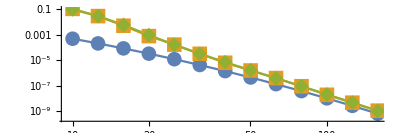

Saved as Lognormal Clayton Estimates.pdf

Times:

* Asymptotics: {0.000274665,0.000187326,0.000185519,0.000169859,0.000166847,0.000154499,0.000149078,0.000167148,0.000173473,0.000140946,0.000138537,0.000137634,0.000140645}

* Polar (R=1e5): {34.280961,32.988887,31.927826,31.048776,25.443455,28.601636,24.788418,24.367394,24.368394,24.389395,24.396395,24.360393,24.336392}

* Asmussen-Kroese (R=1e5): {210.341031,210.050014,210.702052,209.678993,210.183022,210.197023,210.340031,210.471038,210.485039,210.313029,209.661992,209.992011,209.850003}

Estimated Relative errors:

* Polar (R=1e5): {0.0855652,0.108793,0.132252,0.154179,0.181722,0.0715887,0.0594445,0.0419511,0.0658004,0.0634567,0.0269653,0.0263371,0.0408346}

* Asmussen-Kroese (R=1e5): {0.0187682,0.0218678,0.0345483,0.0208081,0.0179292,0.00871253,0.00673222,0.0048081,0.00441188,0.00390515,0.00365584,0.00348312,0.00339112}

ESTIMATED RELATIVE ERRORS PLOT

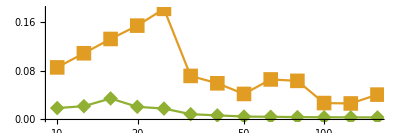

Saved as Lognormal Clayton Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Lognormal Clayton";Print[Name];
γs=10^Range[1,2.25,0.1];
d=12;
μs =-Range[d]/d;
σs=√(Range[d]/d);

Copula={"Clayton",0.9};
Margs=Table[LogNormalDistribution[μs[[i]],σs[[i]]],{i,d}];
𝒟=CopulaDistribution[Copula,Margs];
f[x_]:=CopPDF[Copula,Margs,x]

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>, AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb};
```

Test 6

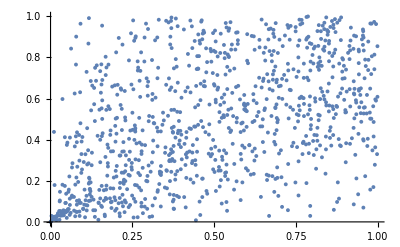

```mathematica
ListPlot[RandomVariate[CopulaDistribution[{"Clayton",0.9},{UniformDistribution[],UniformDistribution[]}],10^3]]
```

Pareto Clayton

[Compare]Asymptotics

[Compare] Completed in 0.000352668 seconds.

[Compare] Asymptotics (0.0000484881 seconds): P(S > 1) estimate is 0.125

[Compare] Asymptotics (0.0000584267 seconds): P(S > 10^(1/4)) estimate is 0.0466307

[Compare] Asymptotics (0.0000397542 seconds): P(S > √10) estimate is 0.0138678

[Compare] Asymptotics (0.0000385496 seconds): P(S > 10^(3/4)) estimate is 0.00344155

[Compare] Asymptotics (0.0000274063 seconds): P(S > 10) estimate is 0.000751315

[Compare] Asymptotics (0.0000382484 seconds): P(S > 10 10^(1/4)) estimate is 0.00015091

[Compare] Asymptotics (0.0000382484 seconds): P(S > 10 √10) estimate is 0.000028803

[Compare] Asymptotics (0.0000376461 seconds): P(S > 10 10^(3/4)) estimate is 5.33377×10^-6

[Compare] Asymptotics (0.0000259005 seconds): P(S > 100) estimate is 9.7059×10^-7

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 1)…

Time to simulate radii: 1.30525

Time to simulate angles: 14.7655

Orig pdf time 4.08422

Angle pdf time = 22.9333

Number of wasted samples = 60610(60.61%)

[PolarEstimator] P(S > 1) estimate: 0.631882. Correction: 5.05505

[PolarEstimator] Estimating P(S > 10^(1/4))…

Time to simulate radii: 1.785

Time to simulate angles: 13.7032

Orig pdf time 3.29641

Angle pdf time = 22.3868

Number of wasted samples = 22092(22.092%)

[PolarEstimator] P(S > 10^(1/4)) estimate: 0.534032. Correction: 11.4524

[PolarEstimator] Estimating P(S > √10)…

Time to simulate radii: 1.67153

Time to simulate angles: 14.62

Orig pdf time 2.97718

Angle pdf time = 23.8769

Number of wasted samples = 2149(2.149%)

[PolarEstimator] P(S > √10) estimate: 0.300725. Correction: 21.6851

[PolarEstimator] Estimating P(S > 10^(3/4))…

Time to simulate radii: 1.87836

Time to simulate angles: 14.6128

Orig pdf time 2.76057

Angle pdf time = 23.9476

Number of wasted samples = 127(0.127%)

[PolarEstimator] P(S > 10^(3/4)) estimate: 0.0189943. Correction: 5.51911

[PolarEstimator] Estimating P(S > 10)…

Time to simulate radii: 1.37482

Time to simulate angles: 14.739

Orig pdf time 2.6183

Angle pdf time = 23.6271

Number of wasted samples = 14(0.014%)

[PolarEstimator] P(S > 10) estimate: 0.00189679. Correction: 2.52463

[PolarEstimator] Estimating P(S > 10 10^(1/4))…

Time to simulate radii: 1.90635

Time to simulate angles: 14.4729

Orig pdf time 1.29838

Angle pdf time = 24.4566

[PolarEstimator] P(S > 10 10^(1/4)) estimate: 0.000191545. Correction: 1.26926

[PolarEstimator] Estimating P(S > 10 √10)…

Time to simulate radii: 1.80055

Time to simulate angles: 14.6683

Orig pdf time 1.34527

Angle pdf time = 24.2587

[PolarEstimator] P(S > 10 √10) estimate: 0.0000364731. Correction: 1.2663

[PolarEstimator] Estimating P(S > 10 10^(3/4))…

Time to simulate radii: 1.92691

Time to simulate angles: 14.6282

Orig pdf time 1.29299

Angle pdf time = 24.5782

[PolarEstimator] P(S > 10 10^(3/4)) estimate: 4.59047×10^-6. Correction: 0.860643

[PolarEstimator] Estimating P(S > 100)…

Time to simulate radii: 1.36435

Time to simulate angles: 14.4862

Orig pdf time 1.29352

Angle pdf time = 24.4699

[PolarEstimator] P(S > 100) estimate: 7.04188×10^-7. Correction: 0.725526

[Compare] Completed in 386.955133 seconds.

[Compare] Polar (R=1e5) (43.8355073 seconds): P(S > 1) estimate is 0.631882

[Compare] Polar (R=1e5) (41.9573998 seconds): P(S > 10^(1/4)) estimate is 0.534032

[Compare] Polar (R=1e5) (43.9255124 seconds): P(S > √10) estimate is 0.300725

[Compare] Polar (R=1e5) (43.970515 seconds): P(S > 10^(3/4)) estimate is 0.0189943

[Compare] Polar (R=1e5) (42.9984593 seconds): P(S > 10) estimate is 0.00189679

[Compare] Polar (R=1e5) (42.6354386 seconds): P(S > 10 10^(1/4)) estimate is 0.000191545

[Compare] Polar (R=1e5) (42.5734351 seconds): P(S > 10 √10) estimate is 0.0000364731

[Compare] Polar (R=1e5) (42.921455 seconds): P(S > 10 10^(3/4)) estimate is 4.59047×10^-6

[Compare] Polar (R=1e5) (42.1374101 seconds): P(S > 100) estimate is 7.04188×10^-7

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 1)…

(AK) Main estimation took: 66.4398

[AKEstimator] Estimating P(S > 10^(1/4))…

(AK) Main estimation took: 66.5204

[AKEstimator] Estimating P(S > √10)…

(AK) Main estimation took: 66.622

[AKEstimator] Estimating P(S > 10^(3/4))…

(AK) Main estimation took: 66.4159

[AKEstimator] Estimating P(S > 10)…

(AK) Main estimation took: 66.0866

[AKEstimator] Estimating P(S > 10 10^(1/4))…

(AK) Main estimation took: 63.3805

[AKEstimator] Estimating P(S > 10 √10)…

(AK) Main estimation took: 66.8362

[AKEstimator] Estimating P(S > 10 10^(3/4))…

(AK) Main estimation took: 66.626

[AKEstimator] Estimating P(S > 100)…

(AK) Main estimation took: 66.2708

[Compare] Completed in 597.384168 seconds.

[Compare] Asmussen-Kroese (R=1e5) (66.6508122 seconds): P(S > 1) estimate is 0.774585

[Compare] Asmussen-Kroese (R=1e5) (66.7718191 seconds): P(S > 10^(1/4)) estimate is 0.587232

[Compare] Asmussen-Kroese (R=1e5) (66.8768252 seconds): P(S > √10) estimate is 0.29159

[Compare] Asmussen-Kroese (R=1e5) (66.6448118 seconds): P(S > 10^(3/4)) estimate is 0.0485734

[Compare] Asmussen-Kroese (R=1e5) (66.3457948 seconds): P(S > 10) estimate is 0.00306596

[Compare] Asmussen-Kroese (R=1e5) (63.6286394 seconds): P(S > 10 10^(1/4)) estimate is 0.000296305

[Compare] Asmussen-Kroese (R=1e5) (67.0778366 seconds): P(S > 10 √10) estimate is 0.0000406364

[Compare] Asmussen-Kroese (R=1e5) (66.8778252 seconds): P(S > 10 10^(3/4)) estimate is 6.42391×10^-6

[Compare] Asmussen-Kroese (R=1e5) (66.5098041 seconds): P(S > 100) estimate is 1.07025×10^-6

Estimates:

* Asymptotics: {0.125,0.0466307,0.0138678,0.00344155,0.000751315,0.00015091,0.000028803,5.33377×10^-6,9.7059×10^-7}

* Polar (R=1e5): {0.631882,0.534032,0.300725,0.0189943,0.00189679,0.000191545,0.0000364731,4.59047×10^-6,7.04188×10^-7}

* Asmussen-Kroese (R=1e5): {0.774585,0.587232,0.29159,0.0485734,0.00306596,0.000296305,0.0000406364,6.42391×10^-6,1.07025×10^-6}

ESTIMATES PLOT

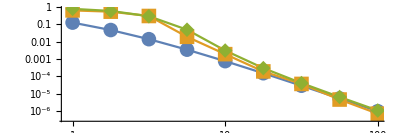

Saved as Pareto Clayton Estimates.pdf

Times:

* Asymptotics: {0.0000484881,0.0000584267,0.0000397542,0.0000385496,0.0000274063,0.0000382484,0.0000382484,0.0000376461,0.0000259005}

* Polar (R=1e5): {43.8355073,41.9573998,43.9255124,43.970515,42.9984593,42.6354386,42.5734351,42.921455,42.1374101}

* Asmussen-Kroese (R=1e5): {66.6508122,66.7718191,66.8768252,66.6448118,66.3457948,63.6286394,67.0778366,66.8778252,66.5098041}

Estimated Relative errors:

* Polar (R=1e5): {0.0545967,0.082178,0.37256,0.15183,0.250725,0.097314,0.168442,0.0913426,0.0776323}

* Asmussen-Kroese (R=1e5): {0.00748519,0.0201388,0.024012,0.0146428,0.0120149,0.00509943,0.00382312,0.00342229,0.00330126}

ESTIMATED RELATIVE ERRORS PLOT

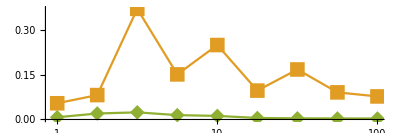

Saved as Pareto Clayton Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Pareto Clayton"; Print[Name];

γs=10^Range[0,2,1/4];
d=16;
Copula={"Clayton",0.9};
Margs=Table[ParetoDistribution[1,2+i,0],{i,d}];
𝒟=CopulaDistribution[Copula,Margs];
f[x_]:=CopPDF[Copula,Margs,x]

(* Note:Mathematica doesn't like TruncatedDistribution with Paretos. So we avoid the built-in truncation method here. *)
RandomRadiusTrunc[γ_,R_]:=SimulateTruncated[MarginalDistribution[𝒟,1],γ,R];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User","𝒟Angles"-> SubexpIndSetup[𝒟],"c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,1],WorkingPrecision-> 50,"R"->R,"SimulateTruncRadius"-> RandomRadiusTrunc|>, AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName->Name,Verbosity-> Verb}
```

Test 7

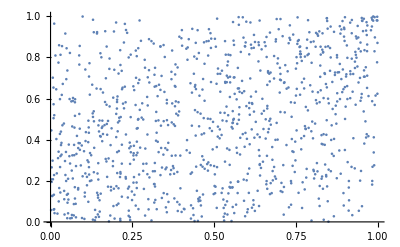

```mathematica
ListPlot[RandomVariate[CopulaDistribution[{"GumbelHougaard",1.25},{UniformDistribution[],UniformDistribution[]}],10^3]]
```

Weibull Heavy Gumbel

[Compare]Asymptotics

[Compare] Completed in 0.00055144 seconds.

[Compare] Asymptotics (0.000109023 seconds): P(S > 10 10^(2/3)) estimate is 0.073523

[Compare] Asymptotics (0.0000578244 seconds): P(S > 100 10^(1/6)) estimate is 0.0307858

[Compare] Asymptotics (0.0000548127 seconds): P(S > 100 10^(2/3)) estimate is 0.00964237

[Compare] Asymptotics (0.0000514998 seconds): P(S > 1000 10^(1/6)) estimate is 0.00205053

[Compare] Asymptotics (0.0000596314 seconds): P(S > 1000 10^(2/3)) estimate is 0.000260205

[Compare] Asymptotics (0.0000569209 seconds): P(S > 10000 10^(1/6)) estimate is 0.0000165862

[Compare] Asymptotics (0.0000548127 seconds): P(S > 10000 10^(2/3)) estimate is 4.22113×10^-7

[Compare] Asymptotics (0.0000542103 seconds): P(S > 100000 10^(1/6)) estimate is 3.15771×10^-9

[Compare] Asymptotics (0.0000527045 seconds): P(S > 100000 10^(2/3)) estimate is 4.61563×10^-12

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10 10^(2/3))…

Time to simulate radii: 1.36341

Time to simulate angles: 11.8046

Orig pdf time 17.0473

Angle pdf time = 29.7366

Number of wasted samples = 20391(20.391%)

[PolarEstimator] P(S > 10 10^(2/3)) estimate: 0.28054. Correction: 3.81568

[PolarEstimator] Estimating P(S > 100 10^(1/6))…

Time to simulate radii: 1.33494

Time to simulate angles: 11.4993

Orig pdf time 16.6234

Angle pdf time = 28.6283

Number of wasted samples = 7924(7.924%)

[PolarEstimator] P(S > 100 10^(1/6)) estimate: 0.112392. Correction: 3.65078

[PolarEstimator] Estimating P(S > 100 10^(2/3))…

Time to simulate radii: 1.33478

Time to simulate angles: 11.5528

Orig pdf time 16.422

Angle pdf time = 28.4531

Number of wasted samples = 2143(2.143%)

[PolarEstimator] P(S > 100 10^(2/3)) estimate: 0.0325844. Correction: 3.3793

[PolarEstimator] Estimating P(S > 1000 10^(1/6))…

Time to simulate radii: 1.33823

Time to simulate angles: 11.6454

Orig pdf time 16.4912

Angle pdf time = 28.6192

Number of wasted samples = 370(0.37%)

[PolarEstimator] P(S > 1000 10^(1/6)) estimate: 0.00553727. Correction: 2.70041

[PolarEstimator] Estimating P(S > 1000 10^(2/3))…

Time to simulate radii: 1.38187

Time to simulate angles: 11.8174

Orig pdf time 15.3567

Angle pdf time = 26.1844

Number of wasted samples = 50(0.05%)

[PolarEstimator] P(S > 1000 10^(2/3)) estimate: 0.00016368. Correction: 0.629045

[PolarEstimator] Estimating P(S > 10000 10^(1/6))…

Time to simulate radii: 1.3442

Time to simulate angles: 11.5744

Orig pdf time 7.3888

Angle pdf time = 18.0052

Number of wasted samples = 1(0.001%)

[PolarEstimator] P(S > 10000 10^(1/6)) estimate: 4.15262×10^-6. Correction: 0.250367

[PolarEstimator] Estimating P(S > 10000 10^(2/3))…

Time to simulate radii: 1.34508

Time to simulate angles: 11.7907

Orig pdf time 1.10987

Angle pdf time = 17.4029

g_S[Ss] time = 1.01527

[PolarEstimator] P(S > 10000 10^(2/3)) estimate: 3.83871×10^-8. Correction: 0.0909403

[PolarEstimator] Estimating P(S > 100000 10^(1/6))…

Time to simulate radii: 1.48165

Time to simulate angles: 12.0231

Orig pdf time 1.1322

Angle pdf time = 16.7682

g_S[Ss] time = 1.01034

[PolarEstimator] P(S > 100000 10^(1/6)) estimate: 6.95817×10^-11. Correction: 0.0220355

[PolarEstimator] Estimating P(S > 100000 10^(2/3))…

Time to simulate radii: 1.44583

Time to simulate angles: 11.8065

Orig pdf time 1.07768

Angle pdf time = 16.4187

[PolarEstimator] P(S > 100000 10^(2/3)) estimate: 1.59384×10^-14. Correction: 0.00345314

[Compare] Completed in 432.171719 seconds.

[Compare] Polar (R=1e5) (61.2955059 seconds): P(S > 10 10^(2/3)) estimate is 0.28054

[Compare] Polar (R=1e5) (59.4333994 seconds): P(S > 100 10^(1/6)) estimate is 0.112392

[Compare] Polar (R=1e5) (59.1063807 seconds): P(S > 100 10^(2/3)) estimate is 0.0325844

[Compare] Polar (R=1e5) (59.4343995 seconds): P(S > 1000 10^(1/6)) estimate is 0.00553727

[Compare] Polar (R=1e5) (56.0912082 seconds): P(S > 1000 10^(2/3)) estimate is 0.00016368

[Compare] Polar (R=1e5) (39.6932703 seconds): P(S > 10000 10^(1/6)) estimate is 4.15262×10^-6

[Compare] Polar (R=1e5) (32.753873 seconds): P(S > 10000 10^(2/3)) estimate is 3.83871×10^-8

[Compare] Polar (R=1e5) (32.51886 seconds): P(S > 100000 10^(1/6)) estimate is 6.95817×10^-11

[Compare] Polar (R=1e5) (31.844821 seconds): P(S > 100000 10^(2/3)) estimate is 1.59384×10^-14

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10 10^(2/3))…

(AK) Main estimation took: 149.479

[AKEstimator] Estimating P(S > 100 10^(1/6))…

(AK) Main estimation took: 150.279

[AKEstimator] Estimating P(S > 100 10^(2/3))…

(AK) Main estimation took: 150.227

[AKEstimator] Estimating P(S > 1000 10^(1/6))…

(AK) Main estimation took: 147.138

[AKEstimator] Estimating P(S > 1000 10^(2/3))…

(AK) Main estimation took: 146.909

[AKEstimator] Estimating P(S > 10000 10^(1/6))…

(AK) Main estimation took: 147.406

[AKEstimator] Estimating P(S > 10000 10^(2/3))…

(AK) Main estimation took: 147.267

[AKEstimator] Estimating P(S > 100000 10^(1/6))…

(AK) Main estimation took: 147.124

[AKEstimator] Estimating P(S > 100000 10^(2/3))…

(AK) Main estimation took: 147.239

[Compare] Completed in 1334.31732 seconds.

[Compare] Asmussen-Kroese (R=1e5) (149.604557 seconds): P(S > 10 10^(2/3)) estimate is 0.286719

[Compare] Asmussen-Kroese (R=1e5) (150.392602 seconds): P(S > 100 10^(1/6)) estimate is 0.126316

[Compare] Asmussen-Kroese (R=1e5) (150.365601 seconds): P(S > 100 10^(2/3)) estimate is 0.0425843

[Compare] Asmussen-Kroese (R=1e5) (147.273424 seconds): P(S > 1000 10^(1/6)) estimate is 0.0102334

[Compare] Asmussen-Kroese (R=1e5) (147.051411 seconds): P(S > 1000 10^(2/3)) estimate is 0.0021423

[Compare] Asmussen-Kroese (R=1e5) (147.56744 seconds): P(S > 10000 10^(1/6)) estimate is 0.000231617

[Compare] Asmussen-Kroese (R=1e5) (147.399431 seconds): P(S > 10000 10^(2/3)) estimate is 8.36425×10^-6

[Compare] Asmussen-Kroese (R=1e5) (147.269423 seconds): P(S > 100000 10^(1/6)) estimate is 1.35398×10^-9

[Compare] Asmussen-Kroese (R=1e5) (147.39343 seconds): P(S > 100000 10^(2/3)) estimate is 7.79397×10^-13

Estimates:

* Asymptotics: {0.073523,0.0307858,0.00964237,0.00205053,0.000260205,0.0000165862,4.22113×10^-7,3.15771×10^-9,4.61563×10^-12}

* Polar (R=1e5): {0.28054,0.112392,0.0325844,0.00553727,0.00016368,4.15262×10^-6,3.83871×10^-8,6.95817×10^-11,1.59384×10^-14}

* Asmussen-Kroese (R=1e5): {0.286719,0.126316,0.0425843,0.0102334,0.0021423,0.000231617,8.36425×10^-6,1.35398×10^-9,7.79397×10^-13}

ESTIMATES PLOT

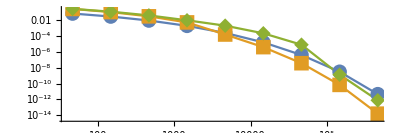

Saved as Weibull Heavy Gumbel Estimates.pdf

Times:

* Asymptotics: {0.000109023,0.0000578244,0.0000548127,0.0000514998,0.0000596314,0.0000569209,0.0000548127,0.0000542103,0.0000527045}

* Polar (R=1e5): {61.2955059,59.4333994,59.1063807,59.4343995,56.0912082,39.6932703,32.753873,32.51886,31.844821}

* Asmussen-Kroese (R=1e5): {149.604557,150.392602,150.365601,147.273424,147.051411,147.56744,147.399431,147.269423,147.39343}

Estimated Relative errors:

* Polar (R=1e5): {0.0377733,0.0848597,0.258107,0.499448,0.0738045,0.0700587,0.101328,0.0784896,0.0663617}

* Asmussen-Kroese (R=1e5): {0.00355027,0.00603079,0.0118351,0.0257027,0.0647652,0.209859,0.838881,0.471507,0.847803}

ESTIMATED RELATIVE ERRORS PLOT

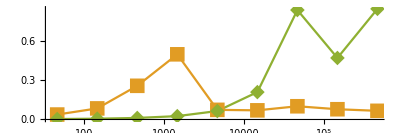

Saved as Weibull Heavy Gumbel Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Weibull Heavy Gumbel";Print[Name];
γs=10^Range[1+2/3,6,1/2];
d=8;
Copula={"GumbelHougaard",1.25};
Margs=Table[WeibullDistribution[1/4,i/d],{i,d}];
𝒟=CopulaDistribution[Copula,Margs];
f[x_]:=CopPDF[Copula,Margs,x]

RandomRadiusTrunc[γ_,R_]:=SimulateTruncated[MarginalDistribution[𝒟,1],γ,R];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],"SimulateTruncRadius"-> RandomRadiusTrunc,
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>,AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb}
```

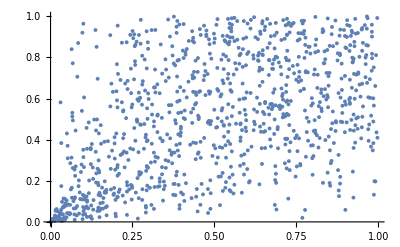

```mathematica
ListPlot[RandomVariate[CopulaDistribution[{"Clayton",0.9},{UniformDistribution[],UniformDistribution[]}],10^3]]
```

Weibull Heavy Clayton

[Compare]Asymptotics

[Compare] Completed in 0.000592097 seconds.

[Compare] Asymptotics (0.000127695 seconds): P(S > 10 10^(2/3)) estimate is 0.073523

[Compare] Asymptotics (0.000059029 seconds): P(S > 100 10^(1/6)) estimate is 0.0307858

[Compare] Asymptotics (0.000057222 seconds): P(S > 100 10^(2/3)) estimate is 0.00964237

[Compare] Asymptotics (0.0000713769 seconds): P(S > 1000 10^(1/6)) estimate is 0.00205053

[Compare] Asymptotics (0.0000502951 seconds): P(S > 1000 10^(2/3)) estimate is 0.000260205

[Compare] Asymptotics (0.0000599325 seconds): P(S > 10000 10^(1/6)) estimate is 0.0000165862

[Compare] Asymptotics (0.0000566197 seconds): P(S > 10000 10^(2/3)) estimate is 4.22113×10^-7

[Compare] Asymptotics (0.000055415 seconds): P(S > 100000 10^(1/6)) estimate is 3.15771×10^-9

[Compare] Asymptotics (0.0000545115 seconds): P(S > 100000 10^(2/3)) estimate is 4.61563×10^-12

[Compare]Polar (R=1e5)

[PolarEstimator] Estimating P(S > 10 10^(2/3))…

Time to simulate radii: 1.38008

Time to simulate angles: 11.7467

Orig pdf time 3.7269

Angle pdf time = 29.939

Number of wasted samples = 20391(20.391%)

[PolarEstimator] P(S > 10 10^(2/3)) estimate: 0.328891. Correction: 4.47332

[PolarEstimator] Estimating P(S > 100 10^(1/6))…

Time to simulate radii: 1.36243

Time to simulate angles: 11.5478

Orig pdf time 3.44082

Angle pdf time = 28.9292

Number of wasted samples = 7924(7.924%)

[PolarEstimator] P(S > 100 10^(1/6)) estimate: 0.167792. Correction: 5.45029

[PolarEstimator] Estimating P(S > 100 10^(2/3))…

Time to simulate radii: 1.40803

Time to simulate angles: 11.6254

Orig pdf time 3.31751

Angle pdf time = 28.8176

Number of wasted samples = 2143(2.143%)

[PolarEstimator] P(S > 100 10^(2/3)) estimate: 0.0523774. Correction: 5.432

[PolarEstimator] Estimating P(S > 1000 10^(1/6))…

Time to simulate radii: 1.38706

Time to simulate angles: 11.5384

Orig pdf time 3.27492

Angle pdf time = 28.6858

Number of wasted samples = 370(0.37%)

[PolarEstimator] P(S > 1000 10^(1/6)) estimate: 0.00907105. Correction: 4.42377

[PolarEstimator] Estimating P(S > 1000 10^(2/3))…

Time to simulate radii: 1.37336

Time to simulate angles: 11.6447

Orig pdf time 3.15606

Angle pdf time = 26.4635

Number of wasted samples = 50(0.05%)

[PolarEstimator] P(S > 1000 10^(2/3)) estimate: 0.00092015. Correction: 3.53625

[PolarEstimator] Estimating P(S > 10000 10^(1/6))…

Time to simulate radii: 1.39171

Time to simulate angles: 11.5232

Orig pdf time 1.68811

Angle pdf time = 18.1875

Number of wasted samples = 1(0.001%)

[PolarEstimator] P(S > 10000 10^(1/6)) estimate: 0.000045942. Correction: 2.7699

[PolarEstimator] Estimating P(S > 10000 10^(2/3))…

Time to simulate radii: 1.36416

Time to simulate angles: 11.5322

Angle pdf time = 15.7416

[PolarEstimator] P(S > 10000 10^(2/3)) estimate: 1.00111×10^-6. Correction: 2.37165

[PolarEstimator] Estimating P(S > 100000 10^(1/6))…

Time to simulate radii: 1.36354

Time to simulate angles: 11.5799

Angle pdf time = 15.9736

[PolarEstimator] P(S > 100000 10^(1/6)) estimate: 6.07089×10^-9. Correction: 1.92256

[PolarEstimator] Estimating P(S > 100000 10^(2/3))…

Time to simulate radii: 1.38251

Time to simulate angles: 11.579

Angle pdf time = 16.0656

[PolarEstimator] P(S > 100000 10^(2/3)) estimate: 7.45733×10^-12. Correction: 1.61567

[Compare] Completed in 357.71946 seconds.

[Compare] Polar (R=1e5) (48.1447537 seconds): P(S > 10 10^(2/3)) estimate is 0.328891

[Compare] Polar (R=1e5) (46.6366675 seconds): P(S > 100 10^(1/6)) estimate is 0.167792

[Compare] Polar (R=1e5) (46.5186607 seconds): P(S > 100 10^(2/3)) estimate is 0.0523774

[Compare] Polar (R=1e5) (46.2316443 seconds): P(S > 1000 10^(1/6)) estimate is 0.00907105

[Compare] Polar (R=1e5) (43.9735151 seconds): P(S > 1000 10^(2/3)) estimate is 0.00092015

[Compare] Polar (R=1e5) (34.143953 seconds): P(S > 10000 10^(1/6)) estimate is 0.000045942

[Compare] Polar (R=1e5) (30.464743 seconds): P(S > 10000 10^(2/3)) estimate is 1.00111×10^-6

[Compare] Polar (R=1e5) (30.750759 seconds): P(S > 100000 10^(1/6)) estimate is 6.07089×10^-9

[Compare] Polar (R=1e5) (30.854765 seconds): P(S > 100000 10^(2/3)) estimate is 7.45733×10^-12

[Compare] Asmussen-Kroese estimator...

[AKEstimator] Estimating P(S > 10 10^(2/3))…

(AK) Main estimation took: 39.5119

[AKEstimator] Estimating P(S > 100 10^(1/6))…

(AK) Main estimation took: 39.2521

[AKEstimator] Estimating P(S > 100 10^(2/3))…

(AK) Main estimation took: 39.3778

[AKEstimator] Estimating P(S > 1000 10^(1/6))…

(AK) Main estimation took: 39.4107

[AKEstimator] Estimating P(S > 1000 10^(2/3))…

(AK) Main estimation took: 39.226

[AKEstimator] Estimating P(S > 10000 10^(1/6))…

(AK) Main estimation took: 39.3783

[AKEstimator] Estimating P(S > 10000 10^(2/3))…

(AK) Main estimation took: 39.2324

[AKEstimator] Estimating P(S > 100000 10^(1/6))…

(AK) Main estimation took: 39.3422

[AKEstimator] Estimating P(S > 100000 10^(2/3))…

(AK) Main estimation took: 39.223

[Compare] Completed in 355.08231 seconds.

[Compare] Asmussen-Kroese (R=1e5) (39.6292667 seconds): P(S > 10 10^(2/3)) estimate is 0.347132

[Compare] Asmussen-Kroese (R=1e5) (39.3712519 seconds): P(S > 100 10^(1/6)) estimate is 0.167503

[Compare] Asmussen-Kroese (R=1e5) (39.5142601 seconds): P(S > 100 10^(2/3)) estimate is 0.050124

[Compare] Asmussen-Kroese (R=1e5) (39.530261 seconds): P(S > 1000 10^(1/6)) estimate is 0.008717

[Compare] Asmussen-Kroese (R=1e5) (39.3612513 seconds): P(S > 1000 10^(2/3)) estimate is 0.000861295

[Compare] Asmussen-Kroese (R=1e5) (39.4972591 seconds): P(S > 10000 10^(1/6)) estimate is 0.0000443308

[Compare] Asmussen-Kroese (R=1e5) (39.355251 seconds): P(S > 10000 10^(2/3)) estimate is 9.35655×10^-7

[Compare] Asmussen-Kroese (R=1e5) (39.4812582 seconds): P(S > 100000 10^(1/6)) estimate is 5.91484×10^-9

[Compare] Asmussen-Kroese (R=1e5) (39.3422502 seconds): P(S > 100000 10^(2/3)) estimate is 7.43904×10^-12

Estimates:

* Asymptotics: {0.073523,0.0307858,0.00964237,0.00205053,0.000260205,0.0000165862,4.22113×10^-7,3.15771×10^-9,4.61563×10^-12}

* Polar (R=1e5): {0.328891,0.167792,0.0523774,0.00907105,0.00092015,0.000045942,1.00111×10^-6,6.07089×10^-9,7.45733×10^-12}

* Asmussen-Kroese (R=1e5): {0.347132,0.167503,0.050124,0.008717,0.000861295,0.0000443308,9.35655×10^-7,5.91484×10^-9,7.43904×10^-12}

ESTIMATES PLOT

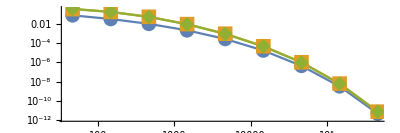

Saved as Weibull Heavy Clayton Estimates.pdf

Times:

* Asymptotics: {0.000127695,0.000059029,0.000057222,0.0000713769,0.0000502951,0.0000599325,0.0000566197,0.000055415,0.0000545115}

* Polar (R=1e5): {48.1447537,46.6366675,46.5186607,46.2316443,43.9735151,34.143953,30.464743,30.750759,30.854765}

* Asmussen-Kroese (R=1e5): {39.6292667,39.3712519,39.5142601,39.530261,39.3612513,39.4972591,39.355251,39.4812582,39.3422502}

Estimated Relative errors:

* Polar (R=1e5): {0.0257951,0.0339394,0.0681122,0.0487813,0.0360566,0.0317796,0.0312997,0.0299492,0.0276296}

* Asmussen-Kroese (R=1e5): {0.00328089,0.00370375,0.00408775,0.0039968,0.00358284,0.00320879,0.00303447,0.00297898,0.0029702}

ESTIMATED RELATIVE ERRORS PLOT

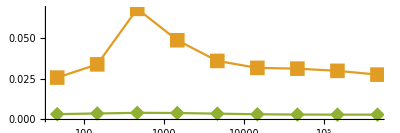

Saved as Weibull Heavy Clayton Estimated REs.pdf

```mathematica
SeedRandom[1337];Name="Weibull Heavy Clayton";Print[Name];
γs=10^Range[1+2/3,6,1/2];
d=8;
Copula={"Clayton",0.9};
Margs=Table[WeibullDistribution[1/4,i/d],{i,d}];
𝒟=CopulaDistribution[Copula,Margs];
f[x_]:=CopPDF[Copula,Margs,x]

RandomRadiusTrunc[γ_,R_]:=SimulateTruncated[MarginalDistribution[𝒟,1],γ,R];

CompareEstimators @@ {f,d,γs,PolarArgs-> <|"𝒟"-> 𝒟,"Angle"-> "User",
"𝒟Angles"-> SubexpIndSetup[𝒟],"SimulateTruncRadius"-> RandomRadiusTrunc,
 "c_S"->1,"𝒟G_S"-> MarginalDistribution[𝒟,d],"R"->R|>,AKArgs-><|"𝒟"-> 𝒟,"R"->R|>,TestName-> Name,Verbosity-> Verb}
```

Plot comparing lognormal asymptotics against reality

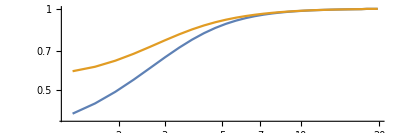

```mathematica
γs=10^Range[0.9,4,0.1];
d=2;
μ ={0,0};
Σ={{1,0},{0,3/4}};
𝒟=LogMultinormalDistribution[μ,Σ];

FirstAsymptotics=Table[SurvivalFunction[MarginalDistribution[𝒟,1],γ],{γ,γs}];
SecondAsymptotics=Table[Sum[SurvivalFunction[MarginalDistribution[𝒟,i],γ],{i,d}],{γ,γs}];

ℓ[γ_] :=  NIntegrate @@
Flatten[{Boole[Total[Table[Subscript[x, i],{i,d}]]>γ]PDF[𝒟,Table[Subscript[x, i],{i,d}]],Table[{Subscript[x, i],0,Infinity},{i,d}],Method->{"GlobalAdaptive", Method-> "MultidimensionalRule"}},1];

NumInts=Table[ℓ[γ],{γ,γs}];

Fig=ListLogLogPlot[{{-Log10[NumInts],FirstAsymptotics / NumInts}ᵀ,{-Log10[NumInts],SecondAsymptotics / NumInts}ᵀ},Joined->True,AspectRatio->1/3,PlotLegends->{"One Term","Two Terms"}];

Print[Fig];
FigName= "Lognormal Asymptotic Comparison.pdf";
Export[FigName,Fig];
```

```mathematica
LinguisticAssistant
```